# Genotype-by-Environment Interactions maintain variation in mutualisms - analysis with symmetric dispersal.

## Setup:

Clear kernel of unwanted junk!

```mathematica
Quit[]
```

Setup dynamical expressions. First, I start by determining the average payoff of each host and symbiont phenotype in each environment:

```mathematica
wh1e1 = HM*s1e1+Hh*(1-s1e1); (*Host 1 environment 1 average payoff is the weighted average of the matching host payoff, and the payoff host 1 receives when interacting with symbiont 2 in environment 1. This means that the host receives a mismatched ρ (symbiont-environment match term) and r (host-symbiont match term)*)
wh2e1 =  Hs*s1e1+Hg*(1-s1e1);
wh1e2=Hg*s1e2+ Hs*(1-s1e2);
wh2e2=Hh*s1e2+HM*(1-s1e2);
```

```mathematica
ws1e1=SM*h1e1+Ss*(1-h1e1);
ws2e1=Sh*h1e1+ Sg*(1-h1e1);
ws1e2= Sg*h1e2+Sh*(1-h1e2);
ws2e2=Ss*h1e2+SM*(1-h1e2);
```

Modified replicator equation to give the frequency of each strategist in each patch and allow dispersal between the patches:

```mathematica
H1E1d=h1e1*(1-h1e1)*(wh1e1-wh2e1)+d*h1e2-d*h1e1;
H1E2d= h1e2*(1-h1e2)*(wh1e2-wh2e2)-d*h1e2+d*h1e1;
S1E1d=s1e1*(1-s1e1)*(ws1e1-ws2e1)+d*s1e2-d*s1e1//Simplify;
S1E2d=s1e2*(1-s1e2)*(ws1e2-ws2e2)-d*s1e2+d*s1e1//Simplify;
```

## Equilibria without dispersal:

When diffusion is equal to 0 it is possible to solve for equilibria:

```mathematica
parameter={d->0};
candidates=Simplify[equilibria=Solve[{H1E1d==0,H1E2d==0,S1E1d==0,S1E2d==0}/.parameter,{h1e1,h1e2,s1e1,s1e2}]]
```

{{h1e1→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e2→0,s1e1→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e2→0},{h1e1→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e2→1,s1e1→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e2→0},{h1e1→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e2→0,s1e1→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e2→1},{h1e1→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e2→1,s1e1→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e2→1},{h1e1→(Sg-Ss)/(Sg-Sh+SM-Ss),h1e2→(-Sh+SM)/(Sg-Sh+SM-Ss),s1e1→(Hg-Hh)/(Hg-Hh+HM-Hs),s1e2→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e1→0,h1e2→(-Sh+SM)/(Sg-Sh+SM-Ss),s1e1→0,s1e2→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e1→1,h1e2→(-Sh+SM)/(Sg-Sh+SM-Ss),s1e1→0,s1e2→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e1→0,h1e2→(-Sh+SM)/(Sg-Sh+SM-Ss),s1e1→1,s1e2→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e1→1,h1e2→(-Sh+SM)/(Sg-Sh+SM-Ss),s1e1→1,s1e2→(HM-Hs)/(Hg-Hh+HM-Hs)},{h1e1→0,h1e2→0,s1e1→0,s1e2→0},{h1e1→1,h1e2→0,s1e1→0,s1e2→0},{h1e1→0,h1e2→1,s1e1→0,s1e2→0},{h1e1→1,h1e2→1,s1e1→0,s1e2→0},{h1e1→0,h1e2→0,s1e1→1,s1e2→0},{h1e1→1,h1e2→0,s1e1→1,s1e2→0},{h1e1→0,h1e2→1,s1e1→1,s1e2→0},{h1e1→1,h1e2→1,s1e1→1,s1e2→0},{h1e1→0,h1e2→0,s1e1→0,s1e2→1},{h1e1→1,h1e2→0,s1e1→0,s1e2→1},{h1e1→0,h1e2→1,s1e1→0,s1e2→1},{h1e1→1,h1e2→1,s1e1→0,s1e2→1},{h1e1→0,h1e2→0,s1e1→1,s1e2→1},{h1e1→1,h1e2→0,s1e1→1,s1e2→1},{h1e1→0,h1e2→1,s1e1→1,s1e2→1},{h1e1→1,h1e2→1,s1e1→1,s1e2→1}}

I can’t analytically solve for my equilibria when there is diffusion:

```mathematica
(*This cell runs forever no matter how many conditions I feed to Solve: *)
(*Simplify[equilibriad=Solve[{{H1E1d,H1E2d,S1E1d,S1E2d}==0,{h1e1,h1e2,s1e1,s1e2}≥0,{h1e1,h1e2,s1e1,s1e2}≤ 1,{hmismatchrθ,hmismatchθρ,himsmatchρr}<hmatch,{smismatchrθ,smismatchθρ,smismatchρr}<smatch},{h1e1,h1e2,s1e1,s1e2},Reals]]*)
```

In a previous analysis I solved for the stability of these equilbria. We understand it quite well. The relative fitness effects of g x g vs g x e interactions changes the outcome of the interaction.

```mathematica
J=Simplify[{
{D[H1E1d, h1e1],D[H1E2d,h1e1],D[S1E1d,h1e1],D[S1E2d,h1e1]},{D[H1E1d, h1e2],D[H1E2d,h1e2],D[S1E1d,h1e2],D[S1E2d,h1e2]},{D[H1E1d, s1e1],D[H1E2d,s1e1],D[S1E1d,s1e1],D[S1E2d,s1e1]},{D[H1E1d, s1e2],D[H1E2d,s1e2],D[S1E1d,s1e2],D[S1E2d,s1e2]}}];
```

Here; however, I'm interested in figuring out the equilibria when there is diffusion. In this instance we cannot exactly solve our system of equations.

## Boundary Equilibria:

### First I’ll try out some boundary equilibria:

What if we just tried out all the boundaries and checked out what happens?

```mathematica
candidates=Tuples[{0,1},4];(*can also plug in candidates from no dispersal case to get same results. *)
(*Evaluate equations at candidates from no dispersal case and return those that are equilibria. *)
equilibrialist={};
Do[{eval={H1E1d,H1E2d,S1E1d,S1E2d}/. {h1e1->candidates[[i,1]],h1e2->1candidates[[i,2]],s1e1->candidates[[i,3]], s1e2->candidates[[i,4]]},If[eval=={0,0,0,0},AppendTo[equilibrialist,candidates[[i]]]]}
,{i,1,Length[candidates]}]
equilibrialist
```

{{0,0,0,0},{0,0,1,1},{1,1,0,0},{1,1,1,1}}

(h1e1,h1e2,s1e1,s1e2)
So there are only two sets of boundary equilibria. One where one genotype fixes everywhere, and another when genotypes and environments mismatch.

```mathematica
(*Equal Frequencies?*)
{H1E1d,H1E2d,S1E1d,S1E2d}/.{h1e1-> 1,h1e2-> 1,s1e1-> 0,s1e2-> 0}//FullSimplify
```

{0,0,0,0}

Let’s evaluate the Jacobian for the mismatching environment, matching genotype equilibrium:

```mathematica
paydiffs={HM->ΔHms+Hs,Hg->ΔHgh+Hh,SM->ΔSmh+Sh,Sg->ΔSgs+Ss};
J/.{h1e1-> 0,s1e1-> 0,h1e2-> 0,s1e2-> 0}/.paydiffs//MatrixForm
J/.{h1e1-> 1,s1e1-> 1,h1e2-> 1,s1e2-> 1}/.paydiffs//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = (J/.{h1e1-> 1,s1e1-> 1,h1e2-> 1,s1e2-> 1})[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-d-ΔHgh | d | 0 | 0
d | -d-ΔHms | 0 | 0
0 | 0 | -d-ΔSgs | d
0 | 0 | d | -d-ΔSmh)

(-d-ΔHms | d | 0 | 0
d | -d-ΔHgh | 0 | 0
0 | 0 | -d-ΔSmh | d
0 | 0 | d | -d-ΔSgs)

{{-d-ΔHms,d},{d,-d-ΔHgh}}

{{-d+Sh-SM,d},{d,-d-Sg+Ss}}

### Global genotypic match: (1,1,1,1), (0,0,0,0)

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r]
CoefficientList[%,r];
a1b1=%[[2]]//FullSimplify
a2b1=%%[[1]]//FullSimplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

r^2+d ΔHgh+d ΔHms+ΔHgh ΔHms+r (2 d+ΔHgh+ΔHms)

2 d+ΔHgh+ΔHms

ΔHgh ΔHms+d (ΔHgh+ΔHms)

If we have a mishmash of the two, we end up somewhere in between.

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r]
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
Collect[%,d]//Simplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

r^2+d Sg-d Sh-Sg Sh+d SM+Sg SM+r (2 d+Sg-Sh+SM-Ss)-d Ss+Sh Ss-SM Ss

2 d+Sg-Sh+SM-Ss

d Sg-d Sh-Sg Sh+d SM+Sg SM-d Ss+Sh Ss-SM Ss

-(Sh-SM) (Sg-Ss)+d (Sg-Sh+SM-Ss)

These are the same stability criteria as the host case, but now in terms of the symbiont parameters. Locally, absolute payoffs must be greater, but in the global case, averages need only be greater.

### Global genotypic mismatch: (1,1,0,0), (0,0,1,1)

```mathematica
J/.{h1e1-> 1,s1e1-> 0,h1e2-> 1,s1e2-> 0}/.paydiffs//MatrixForm
J/.{h1e1-> 0,s1e1-> 1,h1e2-> 0,s1e2-> 1}/.paydiffs//MatrixForm
(*The matrices are in block diagonal form, and the block diagonals of each equilbrium are symmetric. *)
UL=%[[1;;2,1;;2]](*Upper Left Diagonal Matrix*)
LR = (J/.{h1e1-> 1,s1e1-> 1,h1e2-> 1,s1e2-> 1})[[3;;4,3;;4]](*Lower Right Diagonal Matrix*)
```

(-d+Hgh | d | 0 | 0
d | -d+HM-Hs | 0 | 0
0 | 0 | -d-Sh+SM | d
0 | 0 | d | -d+Sgs)

(-d+HM-Hs | d | 0 | 0
d | -d+Hgh | 0 | 0
0 | 0 | -d+Sgs | d
0 | 0 | d | -d-Sh+SM)

{{-d+HM-Hs,d},{d,-d+Hgh}}

{{-d+Sh-SM,d},{d,-d-Sg+Ss}}

```mathematica
CharacteristicPolynomial[UL,r];
Collect[%,r]
CoefficientList[%,r];
a1b1=%[[2]]//FullSimplify
a2b1=%%[[1]]//FullSimplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

-d Hgh-d HM+Hgh HM+d Hs-Hgh Hs+(2 d-Hgh-HM+Hs) r+r^2

2 d-Hgh-HM+Hs

Hgh (HM-Hs)-d (Hgh+HM-Hs)

If we have a mishmash of the two, we end up somewhere in between.

```mathematica
CharacteristicPolynomial[LR,r];
Collect[%,r]
CoefficientList[%,r];
a1=%[[2]]
a2=%%[[1]]
Collect[%,d]//Simplify
(*Our characteristic polynomial is now in the form r^2+a1*r+a2=0. Using the routh hurwitz criterion our equilibrium will be locally stable when a1>0 and a2>0. Let's see what these criteria look like: *)
```

r^2+d Sg-d Sh-Sg Sh+d SM+Sg SM+r (2 d+Sg-Sh+SM-Ss)-d Ss+Sh Ss-SM Ss

2 d+Sg-Sh+SM-Ss

d Sg-d Sh-Sg Sh+d SM+Sg SM-d Ss+Sh Ss-SM Ss

-(Sh-SM) (Sg-Ss)+d (Sg-Sh+SM-Ss)

## Approximations:

### Itty bitty dispersal approximation of equilibria to the first order:

First, we’ll approximate the equilibria:

```mathematica
(*Try defining each variable as a taylor series and give it a go!!*)
 assumptionfn[x_] := x/.{d-> d*ϵ,h1e1->h1e10+ h1e11*ϵ,h1e2-> h1e20+h1e21*ϵ,s1e1->s1e10+s1e11* ϵ, s1e2->s1e20+s1e21* ϵ};
{H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
Series[%,{ϵ,0,0}]//Normal(*0th Order Approximation*);
ans=Solve[%==0,{h1e10,h1e20,s1e10,s1e20}];
```

Our 0th order equilibria are the same as those for the no dispersal case. 
Next,  we’ll plug those 0 order cases into the 0 and first order expansion, and then solve for the first order terms. 
I’ll sum the 0 order and first order terms and store them in the ApproximatedEq object.

```mathematica
ApproximatedEq={};
Do[{sys={H1E1d,H1E2d,S1E1d,S1E2d}//assumptionfn//Factor;
exp=Series[sys,{ϵ,0,1}]//Normal(*First Order Approximation*);
eval=exp/.ans[[i]]//Factor;
firstorder=Solve[eval==0,{h1e11,h1e21,s1e11,s1e21}]//Factor;
approximated={};
Do[eqi=ans[[ i,j,2]]+firstorder[[1,j,2]];
AppendTo[approximated,eqi],{j,1,4}];
AppendTo[ApproximatedEq,approximated]},{i,1,Length[ans]}]


ApproximatedEq//FullSimplify;
```

all in form: (h1e1,h1e2,s1e1,s1e2): Numerical case to check which equilibria might actually fit our constraints:

So we can throw out some of the equilibria based on the 0th order terms! Terms 2,3, 7,8,11,12,13,14,16,17,18,19,21,22,23, and 24 are not near the border between stability and instability. Their 0th order eigenvalue approximations involve the difference between a positive Matching payoff (SM or HM) and a negative mismatched payoff. They will always be positive and unstable for small d.  

We can also throw out even more terms! But there are instances where this will be on the border between stability and instability if any one set of the mismatched payoffs are equal. 

Let’s select the instances whose stability remains unknown:

```mathematica
unstables={2,3,7,8,11,12,13,14,16,17,18,19,21,22,23,24};(*List of equilibria that must be unstable. *)
filteredeq={};
Do[If[ContainsAny[{i},unstables]==False,AppendTo[filteredeq,ApproximatedEq[[i]]]],{i,1,Length[ApproximatedEq]}]
filteredeq;
```

#### Stability of approximate equilibria:

Here, I’ll pick out the equilirium I think is most likely to be stable, and approximate its stability criterion:

```mathematica
JC =J/.{h1e1->1+d/(-HM+Hs),h1e2-> d/(HM-Hs),s1e1-> 1+d/(Sh-SM),s1e2->d/(-Sh+SM)}/.d-> d*ϵ;
(*Evaluate the Jacobian at the equilirium of interest and apply our assumption that dispersal is itty bitty. Note that the change of variables doesn't matter so much here since we have values for the frequencies from our earlier approximation. All we're really doing here is d -> d*ϵ. *)
charpoly=CharacteristicPolynomial[JC,λ];
charpolyexp=charpoly/.{λ-> λ0+λ1*ϵ};
(*First we set ϵ = 0 and solve our characteristic polynomial for our eigenvalues. This gives an approximation of the eigenvalues to the 0th order, with our small parameter (d) equal to 0: *)
b=Series[charpolyexp,{ϵ,0,0}]//Normal;
Othorderλs=Solve[b==0,λ0]
(*These are the 0th order values of λ. We don't really need to go to higher orders because they're all negative! Hooray! None of them are on the border between stability and instability. But let's go higher as an exercise. *)
a=Series[charpolyexp,{ϵ,0,1}]//Normal ;
firstorders={};
Do[AppendTo[firstorders,a/.Othorderλs[[i]]],{i,1,4}]
(* Here, I'm solving the first order taylor series expansion, using each of the λ0 terms I found earlier. *)
firstorders
Othorderλs[[1;;4,1,2]]
(* this expression is analagous to 8.49 in Otto and Day pp. 336. Also see the univariate details for this procedure on 183 and 184. 
The first order terms are all 0. *)
```

{{λ0→-HM+Hs},{λ0→-HM+Hs},{λ0→Sh-SM},{λ0→Sh-SM}}

{0,0,0,0}

{-HM+Hs,-HM+Hs,Sh-SM,Sh-SM}

### Stability of candidate equilibria:

#### Second Internal equilibrium: Unstable:

```mathematica
StabilityofEQCOV[filteredeq[[2]]]
```

{{(-d (ΔHgh+ΔHms)+ΔHgh ΔSgs)/(ΔHgh (ΔSgs+ΔSmh)),1-(d ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(ΔHgh ΔSgs-d (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSgs),1-(d ΔHms)/((ΔHgh+ΔHms) ΔSgs)},{{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}},{λ1→d (1+ΔHms/ΔSgs-(2 ΔSgs)/(ΔSgs+ΔSmh)),λ1→d (1-(2 ΔHgh)/(ΔHgh+ΔHms)+ΔSmh/ΔHgh),λ1→-((d (ΔHms^(5/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh)+ΔHgh^2 √ΔHms ΔSmh^(3/2) (ΔSgs+ΔSmh)+ΔHgh ΔHms^(3/2) √ΔSmh (ΔSgs+ΔSmh)^2+√ΔHgh ΔHms √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)-ΔSmh (ΔSgs+ΔSmh))+ΔHgh^(3/2) √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)+ΔSmh (ΔSgs+ΔSmh))))/(2 ΔHgh √ΔHms (ΔHgh+ΔHms) ΔSgs √ΔSmh (ΔSgs+ΔSmh))),λ1→-((d (ΔHms^(5/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh)+ΔHgh^2 √ΔHms ΔSmh^(3/2) (ΔSgs+ΔSmh)+ΔHgh ΔHms^(3/2) √ΔSmh (ΔSgs+ΔSmh)^2-ΔHgh^(3/2) √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)+ΔSmh (ΔSgs+ΔSmh))+√ΔHgh ΔHms √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (-ΔSgs+ΔSmh)+ΔSmh (ΔSgs+ΔSmh))))/(2 ΔHgh √ΔHms (ΔHgh+ΔHms) ΔSgs √ΔSmh (ΔSgs+ΔSmh)))}}

The third and fourth 0th order eigenvalue approximations can be re-written in terms of the second and fourth equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

λ0=±√(((1-h1e2) ΔH2 ΔH2 (1-s1e2)ΔS2 ΔS2)/(d d)=)±(ΔH2 ΔS2)/d √((1-h1e2)(1- s1e2))

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Third Internal equilibrium: Unstable:

```mathematica
StabilityofEQCOV[filteredeq[[3]]]
```

Part::take: Cannot take positions 1 through 4 in {}.

{{(d ΔHgh^2-d ΔHms^2+ΔHgh ΔHms ΔSgs)/(ΔHgh ΔHms ΔSgs+ΔHgh ΔHms ΔSmh),(d (-ΔHgh^2+ΔHms^2)+ΔHgh ΔHms ΔSmh)/(ΔHgh ΔHms (ΔSgs+ΔSmh)),(d ΔSgs^2+ΔHgh ΔSgs ΔSmh-d ΔSmh^2)/(ΔHgh ΔSgs ΔSmh+ΔHms ΔSgs ΔSmh),(ΔHms ΔSgs ΔSmh+d (-ΔSgs^2+ΔSmh^2))/((ΔHgh+ΔHms) ΔSgs ΔSmh)},{{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}},{}}

This equilibrium is always unstable (outside of the 0 difference case):

if all Δ’s are positive, it cannot be stable

if just one Δ is negative (ΔH2 or ΔS2) ΔH1 + ΔH2 or ΔS1 + ΔS2 determine existence / stability. If either sum is less than 0, the equilibrium will exist but be unstable. If either sum is greater than 0 the equilibrium cannot exist.

if  ΔH2 AND ΔS2 are negative, it can only exist if ΔH1 + ΔH2 and ΔS1 +ΔS2 are less than 0, in which case it cannot be stable.

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Fourth Internal equilibrium: Unstable:

```mathematica
StabilityofEQCOV[filteredeq[[4]]]
```

{{(d ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(d (ΔHgh+ΔHms)+ΔHgh ΔSmh)/(ΔHgh (ΔSgs+ΔSmh)),(d ΔHms)/((ΔHgh+ΔHms) ΔSgs),(ΔHms ΔSgs+d (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSgs)},{{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}},{λ1→d (1+ΔHms/ΔSgs-(2 ΔSgs)/(ΔSgs+ΔSmh)),λ1→d (1-(2 ΔHgh)/(ΔHgh+ΔHms)+ΔSmh/ΔHgh),λ1→-((d (ΔHms^(5/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh)+ΔHgh^2 √ΔHms ΔSmh^(3/2) (ΔSgs+ΔSmh)+ΔHgh ΔHms^(3/2) √ΔSmh (ΔSgs+ΔSmh)^2+√ΔHgh ΔHms √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)-ΔSmh (ΔSgs+ΔSmh))+ΔHgh^(3/2) √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)+ΔSmh (ΔSgs+ΔSmh))))/(2 ΔHgh √ΔHms (ΔHgh+ΔHms) ΔSgs √ΔSmh (ΔSgs+ΔSmh))),λ1→-((d (ΔHms^(5/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh)+ΔHgh^2 √ΔHms ΔSmh^(3/2) (ΔSgs+ΔSmh)+ΔHgh ΔHms^(3/2) √ΔSmh (ΔSgs+ΔSmh)^2-ΔHgh^(3/2) √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)+ΔSmh (ΔSgs+ΔSmh))+√ΔHgh ΔHms √ΔSgs √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (-ΔSgs+ΔSmh)+ΔSmh (ΔSgs+ΔSmh))))/(2 ΔHgh √ΔHms (ΔHgh+ΔHms) ΔSgs √ΔSmh (ΔSgs+ΔSmh)))}}

Now third and fourth 0th order eigenvalue approximations can be re-written in terms of the first and third equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))},{λ0→(√ΔH1 √ΔH2 √ΔS1 √ΔS2)/(√((ΔH1+ΔH2) (ΔS1+ΔS2)))}}

λ0=±√((h1e1 ΔH2 ΔH2 s1e1 ΔS2ΔS2)/(d d)=)±(ΔH2 ΔS2)/d √(h1e1 s1e1)

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Fifth Internal equilibrium: Unstable:

```mathematica
StabilityofEQCOV[filteredeq[[5]]]
```

{{1-(d ΔSgs)/(ΔHms (ΔSgs+ΔSmh)),(-d (ΔHgh+ΔHms)+ΔHms ΔSmh)/(ΔHms (ΔSgs+ΔSmh)),1-(d ΔHgh)/((ΔHgh+ΔHms) ΔSmh),(ΔHms ΔSmh-d (ΔSgs+ΔSmh))/((ΔHgh+ΔHms) ΔSmh)},{{λ0→-ΔHms},{λ0→-ΔSmh},{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}},{λ1→(d ΔHgh)/ΔSmh+(d (ΔSgs-ΔSmh))/(ΔSgs+ΔSmh),λ1→(d (ΔHgh-ΔHms))/(ΔHgh+ΔHms)+(d ΔSgs)/ΔHms,λ1→-((d (√ΔHgh ΔHms^2 ΔSgs^(3/2) (ΔSgs+ΔSmh)+ΔHgh^(5/2) √ΔSgs ΔSmh (ΔSgs+ΔSmh)+ΔHgh^(3/2) ΔHms √ΔSgs (ΔSgs+ΔSmh)^2+ΔHgh^2 √ΔHms √ΔSmh (-ΔSgs+ΔSmh) √((ΔHgh+ΔHms) (ΔSgs+ΔSmh))+ΔHms^(3/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh) √((ΔHgh+ΔHms) (ΔSgs+ΔSmh))+ΔHgh √ΔHms √ΔSmh √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (-ΔSgs+ΔSmh)-ΔSgs (ΔSgs+ΔSmh))))/(2 √ΔHgh ΔHms (ΔHgh+ΔHms) √ΔSgs ΔSmh (ΔSgs+ΔSmh))),λ1→-((d (√ΔHgh ΔHms^2 ΔSgs^(3/2) (ΔSgs+ΔSmh)+ΔHgh^(5/2) √ΔSgs ΔSmh (ΔSgs+ΔSmh)+ΔHgh^(3/2) ΔHms √ΔSgs (ΔSgs+ΔSmh)^2+ΔHgh^2 √ΔHms (ΔSgs-ΔSmh) √ΔSmh √((ΔHgh+ΔHms) (ΔSgs+ΔSmh))-ΔHms^(3/2) ΔSgs √ΔSmh (ΔSgs+ΔSmh) √((ΔHgh+ΔHms) (ΔSgs+ΔSmh))+ΔHgh √ΔHms √ΔSmh √((ΔHgh+ΔHms) (ΔSgs+ΔSmh)) (ΔHms (ΔSgs-ΔSmh)+ΔSgs (ΔSgs+ΔSmh))))/(2 √ΔHgh ΔHms (ΔHgh+ΔHms) √ΔSgs ΔSmh (ΔSgs+ΔSmh)))}}

Now third and fourth 0th order eigenvalue approximations can be re-written in terms of the first and third equilibria!

```mathematica
Othorderλs[[3;;4]]
```

{{λ0→-(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))},{λ0→(√ΔHgh √ΔHms √ΔSgs √ΔSmh)/(√((ΔHgh+ΔHms) (ΔSgs+ΔSmh)))}}

λ0=±√(((1-h1e2) ΔH1 ΔH1 (1-s1e1)ΔS1 ΔS1)/(d d)=)±(ΔH1 ΔS1)/d √((1-h1e1)(1- s1e1))

Once again, if the equilibrium exists it must be unstable unless a Δ term equals 0.

#### Sixth boundary equilibrium (0,0,0,0) (global genotypic match): Stable when ΔHgh and ΔSgs are positive, stability increases with increasing d. Matches analytical results.

```mathematica
StabilityofEQCOV[filteredeq[[6]]]
```

{{0,0,0,0},{{λ0→-ΔHgh},{λ0→-ΔHms},{λ0→-ΔSgs},{λ0→-ΔSmh}},{λ1→-d,λ1→-d,λ1→-d,λ1→-d}}

Stable if -ΔHgs and -ΔHgh are positive, which matches our intuition for this boundary equilibrium.

#### Seventh internal equilibrium (migration-selection balance): Always stable.

```mathematica
StabilityofEQCOV[filteredeq[[7]]]
```

Part::take: Cannot take positions 1 through 4 in {}.

{{1-d/ΔHms,d/ΔHms,1-d/ΔSmh,d/ΔSmh},{{λ0→-ΔHms},{λ0→-ΔHms},{λ0→-ΔSmh},{λ0→-ΔSmh}},{}}

#### Eighth internal equilibrium (reverse migration selection balance): Conditionally stable.

```mathematica
StabilityofEQCOV[filteredeq[[8]]]
```

Part::take: Cannot take positions 1 through 4 in {}.

{{d/ΔHgh,1-d/ΔHgh,d/ΔSgs,1-d/ΔSgs},{{λ0→-ΔHgh},{λ0→-ΔHgh},{λ0→-ΔSgs},{λ0→-ΔSgs}},{}}

#### Ninth equilibrium (1,1,1,1) (global genotypic match): Stable if Hg>Hh and Sg>Ss. Increasing stability with increasing dispersal.

```mathematica
StabilityofEQCOV[filteredeq[[9]]]
```

{{1,1,1,1},{{λ0→-ΔHgh},{λ0→-ΔHms},{λ0→-ΔSgs},{λ0→-ΔSmh}},{λ1→-d,λ1→-d,λ1→-d,λ1→-d}}

## Simulations of Single Trajectories:

```mathematica
dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:= {h1e1'[t]==-d h1e1[t]+d h1e2[t]+(1-h1e1[t]) h1e1[t] (-Hg (1-s1e1[t])+Hh (1-s1e1[t])+HM s1e1[t]-Hs s1e1[t]),h1e2'[t]==d h1e1[t]-d h1e2[t]+(1-h1e2[t]) h1e2[t] (-HM (1-s1e2[t])+Hs (1-s1e2[t])+Hg s1e2[t]-Hh s1e2[t]),s1e1'[t]==-d s1e1[t]+(Ss (1-h1e1[t])+Sg (-1+h1e1[t])-Sh h1e1[t]+SM h1e1[t]) (1-s1e1[t]) s1e1[t]+d s1e2[t],s1e2'[t]==d s1e1[t]-d s1e2[t]+(Sh (1-h1e2[t])-SM (1-h1e2[t])+Sg h1e2[t]-Ss h1e2[t]) (1-s1e2[t]) s1e2[t],h1e1[0]==h1e10,h1e2[0]==h1e20,s1e1[0]==s1e10,s1e2[0]==s1e20}
```

#### Solve parametrically and vary dispersal:

```mathematica
dynsol=ParametricNDSolveValue[dynsys[0.5,0.59,0.41,0.5,2,1,1,1,2,1,1,1],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,50},{d}];
```

Try out some values of dispersal:

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.8,0.1}];
h1e1v=fxntable[[All,2,1]];
h1e2v=fxntable[[All,2,2]];
cols=fxntable[[All,1]];
stratlist={"h1e1","h1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
```

```mathematica
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
```

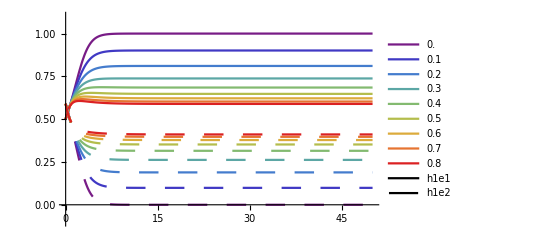

```mathematica
Legended[Plot[{h1e1v,h1e2v},{t,0,50},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

Let’s try engineering conditions that would favor a boundary equilibrium. Here Hg=Hs=Sg=Ss and all are larger than Hs and Ss. Our analytical work predicts that this scenario will lead to either: the boundary equilibrium with one host one symbiont globally, or the internal polymorphic equilibrium.

```mathematica
(*[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[0.55,0.44,0.6,0.1,2,1.8,1,1.8,2,1.8,1,1.8],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,100},{d}]
```

ParametricFunction[<>]

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.2,0.04}];
```

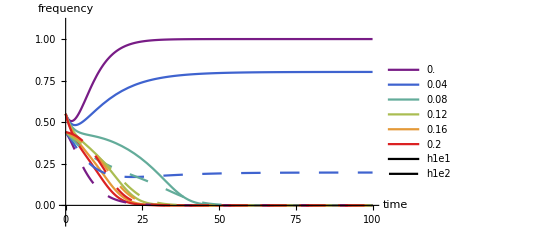

```mathematica
h1e1v=fxntable[[All,2,1]];
h1e2v=fxntable[[All,2,2]];
cols=fxntable[[All,1]];
stratlist={"h1e1","h1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
myplot=Legended[Plot[{h1e1v,h1e2v},{t,0,100},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ,AxesLabel->{"time","frequency"}], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

```mathematica
fxntable=Table[{di,dynsol[di]},{di,0,0.2,0.04}];
```

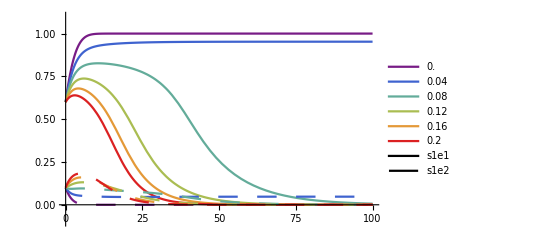

```mathematica
s1e1v=fxntable[[All,2,3]];
s1e2v=fxntable[[All,2,4]];
cols=fxntable[[All,1]];
stratlist={"s1e1","s1e2"};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]],ColorData["Rainbow"][(j-1)/(Length[cols]-1)]},{i,1,Length[stratlist]},{j,1,Length[cols]}]~Flatten~1;
Legended[Plot[{s1e1v,s1e2v},{t,0,100},PlotRange->{-0.1,1.1},PlotStyle->aestable,PlotLegends-> cols ], LineLegend[{linelist[[1]],linelist[[2]]},stratlist]]
```

```mathematica
pi1=0.1;
pi2=-0.7;
(*[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h0,h0,s0,s0,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,500},{d,h0,s0}]
```

ParametricFunction[<>]

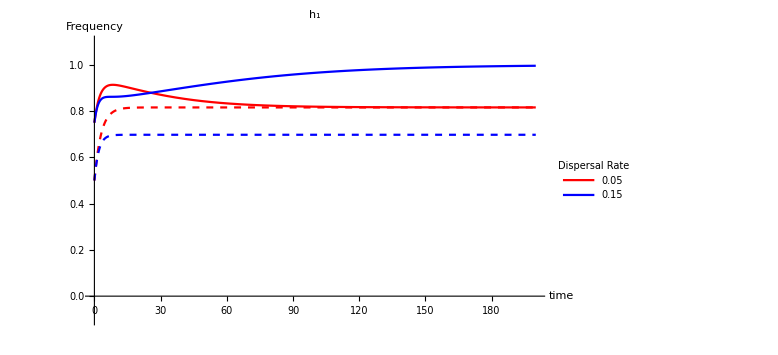

```mathematica
fxntable=Table[{{di,h0},dynsol[di,h0,s0]},{di,{0.05,0.15}},{h0,{0.5,0.75}},{s0,{0.5}}];
fxntable2=Flatten[fxntable,2];
h1e1v=fxntable2[[All,2,1]];
h1e2v=fxntable2[[All,2,2]];
s1e1v=fxntable2[[All,2,3]];
s1e2v=fxntable2[[All,2,4]];
cols=fxntable2[[All,1]];
stratlist={"h1e1","h1e2"};
dlist={0.05,0.15};
linelist={Default,Dashing[{Large,Large}],Dashed,Dotted};
aestable=Table[{linelist[[i]]},{i,1,Length[linelist]}]~Flatten~1;
myplot=Legended[Plot[{h1e1v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Red,Thick,Dashed},{Red,Thick},{Blue,Thick,Dashed},{Blue,Thick}},AxesLabel->{"time","Frequency"},PlotLabel-> "h_1",AxesStyle->Thick,LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black} ,ImageSize->Large], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate",LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black}]]
(*Export["host1plot.png",myplot];*)
```

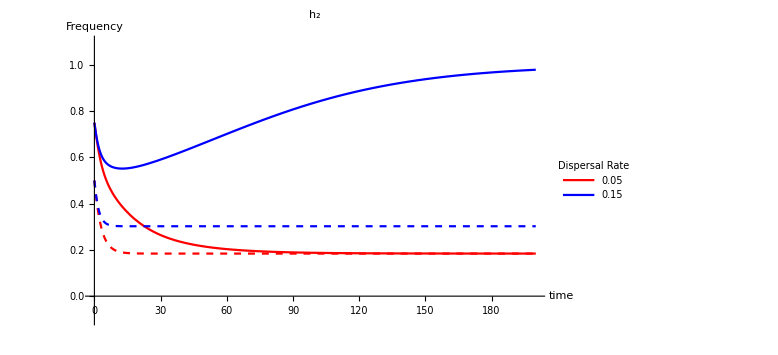

```mathematica
host2plot=Legended[Plot[{h1e2v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Red,Thick,Dashed},{Red,Thick},{Blue,Thick,Dashed},{Blue,Thick}},AxesLabel->{"time","Frequency"},PlotLabel-> "h_2",AxesStyle->Thick,LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black} ,ImageSize->Large ], LineLegend[{Red,Blue},{"0.05","0.15"},LegendLabel->"Dispersal Rate"]]
(*Export["host2plot.png",host2plot]*)
```

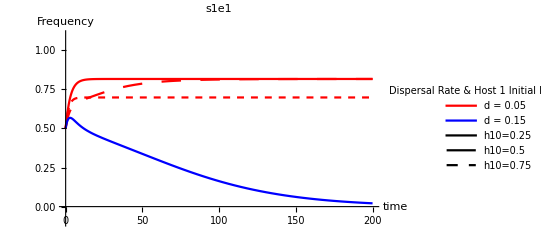

```mathematica
Legended[Plot[{s1e1v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e1" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

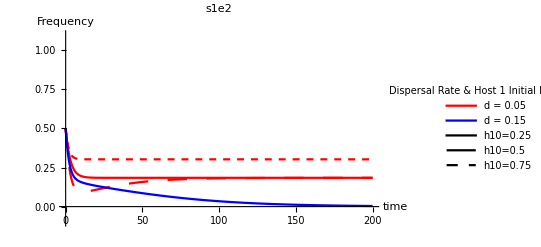

```mathematica
Legended[Plot[{s1e2v},{t,0,200},PlotRange->{-0.1,1.1},PlotStyle->{{Default,Red},{Dashing[{Large,Large}],Red},{Dashed,Red},{Default,Blue},{Dashing[{Large,Large}],Blue},{Dashed,Blue}},AxesLabel->{"time","Frequency"},PlotLabel-> "s1e2" ], LineLegend[{Red,Blue,Default,Dashing[{Large,Large}],Dashed},{"d = 0.05","d = 0.15","h10=0.25","h10=0.5","h10=0.75"},LegendLabel->"Dispersal Rate & Host 1 Initial Frequency"]]
```

```mathematica
pi1=0.3;
pi2=0.7;
(*[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h0,h0,s0,s0,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2],{h1e1[t],h1e2[t],s1e1[t],s1e2[t]},{t,0,500},{d,h0,s0}]
```

ParametricFunction[<>]

## Numerical Simulations of Many Trajectories :

### Functions for simulation analysis:

A function that plots final frequencies of hosts and symbionts after 10000 units of time.

```mathematica
dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:= {h1e1'[t]==-d h1e1[t]+d h1e2[t]+(1-h1e1[t]) h1e1[t] (-Hg (1-s1e1[t])+Hh (1-s1e1[t])+HM s1e1[t]-Hs s1e1[t]),h1e2'[t]==d h1e1[t]-d h1e2[t]+(1-h1e2[t]) h1e2[t] (-HM (1-s1e2[t])+Hs (1-s1e2[t])+Hg s1e2[t]-Hh s1e2[t]),s1e1'[t]==-d s1e1[t]+(Ss (1-h1e1[t])+Sg (-1+h1e1[t])-Sh h1e1[t]+SM h1e1[t]) (1-s1e1[t]) s1e1[t]+d s1e2[t],s1e2'[t]==d s1e1[t]-d s1e2[t]+(Sh (1-h1e2[t])-SM (1-h1e2[t])+Sg h1e2[t]-Ss h1e2[t]) (1-s1e2[t]) s1e2[t],h1e1[0]==h1e10,h1e2[0]==h1e20,s1e1[0]==s1e10,s1e2[0]==s1e20}

PlotWFN[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_,dmax_,deltad_]:={tmax=10000;
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e20,s1e10,s1e20,HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->5,PrecisionGoal->3];
(*Solve dynamical system and store the final value of the frequency of each symbiont at time tmax for each initial frequency that is imputed to the function. *)
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,dmax,deltad}]~Flatten~1;
ds=fxntable2[[All,1]];
averagef=fxntable2[[All,2]];
h1e1v=fxntable2[[All,3,1]];
h1e2v=fxntable2[[All,3,2]];
s1e1v=fxntable2[[All,3,3]];
s1e2v=fxntable2[[All,3,4]];
h1e1p=Transpose@{ds,averagef,h1e1v};
h1e2p=Transpose@{ds,averagef,h1e2v};
s1e1p=Transpose@{ds,averagef,s1e1v};
s1e2p=Transpose@{ds,averagef,s1e2v};
(*Transform tables of final frequencies for plotting.  *)
stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h2",h1e2p},{"s2",s1e2p}};
plotlist={};
(*Plot final frequency of each host and symbiont*)
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-deltad,dmax+deltad},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];
Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

A function that plots the model’s possible equilbiria and their stability:

```mathematica
fitnessfxnSym[HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_,pi1_,pi2_]:=
{(*Value of matched internal equilibrium*)
Plot[{1-d/pi1,d/pi1},{d,0,0.5},PlotStyle->{Red,Blue},PlotLabel-> "Migration Selection Balance Equilibrium value",PlotLabels->{"1-d/Δπ1 in matched env","d/Δπ1in mismatched env"}, ImageSize-> Large],
(*Migration Selection balance *)Plot[{((d/(SM-Sh))*Hh+(1-(d/(SM-Sh)))* HM),((d/(SM-Sh))*Hg+(1-(d/(SM-Sh)))* Hs),Mean[{((d/(SM-Sh))*Hh+(1-(d/(SM-Sh)))* HM),((d/(SM-Sh))*Hg+(1-(d/(SM-Sh)))* Hs)}]},{d,0,0.5},PlotLabel-> "Migration Selection Balance Host Fitness",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium,PlotRange->{0,2}],
(*Value of mis-matched internal equilibrium*)
Plot[{d/pi2,1-d/pi2},{d,0,0.5},PlotStyle->{Red,Blue},PlotLabel-> "Reverse Migration Selection Balance Equilibrium value",PlotLabels->{"d/Δπ2in matched env","1-d/Δπ2 in mismatched env"}, ImageSize-> Large],
(*Reverse Migration Selection Balance*)
Plot[{((d/(pi2))*HM+(1-(d/(Sg-Ss)))* Hh),((d/(Sg-Ss))*Hs+(1-(d/(Sg-Ss)))* Hg),Mean[{((d/(Sg-Ss))*HM+(1-(d/(Sg-Ss)))* Hg),((d/(Sg-Ss))*Hs+(1-(d/(Sg-Ss)))* Hh)}]},{d,0,0.5},PlotLabel-> "Reverse Migration Selection Balance Host Fitness",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium,PlotRange->{0,2}],
(*Value of Routh-Hurwitz criterion for mismatched boundary equilibrium*)
Plot[{2d-(pi1+pi2),pi1*pi2-d(pi1+pi2)},{d,0,0.5},PlotLabel-> "Routh-Hurwitz mismatched boundary",PlotLabels->{"a1","a2"},ImageSize-> Medium],
(*Global Mismatch*)
Plot[{Hh,Hs,Mean[{Hh,Hs}]},{d,0,0.5},PlotLabel-> "Global Mismatch Host Fitness",PlotLabels->{"e1","e2","Mean"},PlotRange->{0,2},ImageSize->Medium],
(*Value of Routh-Hurwitz criterion for matched boundary equilibrium*)
Plot[{2d+(pi1+pi2),pi1*pi2+d(pi1+pi2)},{d,0,0.5},PlotLabel-> "Routh-Hurwitz matched boundary",PlotLabels->{"a1","a2"},ImageSize-> Medium],
(*Global Match*)
Plot[{HM,Hg,Mean[{HM,Hg}]},{d,0,0.5},PlotLabel-> "Global Match Host Fitness",PlotLabels->{"e1","e2","Mean"},PlotRange->{0,2},ImageSize->Medium]
}
```

Here, let’s compare the fitness advantage across environments using an additional function that compares fitness within and between environments:

```mathematica
fitnessfxn3[HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:=
{(*Host 1 Fitness*)
w1=s1*HM+(1-s1)*Hh;
w2=s1*Hg+(1-s1)*Hs;
Plot[{w1,w2,Mean[{w1,w2}]},{s1,0,1},AxesLabel->{"symbiont 1 frequency","Host 1 fitness"},LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large],PlotLabel-> "host 1 local fitness",PlotLabels->{"e1","e2","Mean"},ImageSize->Large],
(*Host 1 Fitness variation in Symbiont Frequency*)
averageWg1=Table[{se1,se2,w1=se1*HM+(1-se1)*Hh;w2=se2*Hg+(1-se2)*Hs;Mean[{w1,w2}]},{se1, 0,1,0.01},{se2,0,1,0.01}];
averageWg1p=Flatten[averageWg1,1];
ListDensityPlot[averageWg1,Frame->True,FrameLabel->{"s1e1","s1e2"},PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "Rainbow",InterpolationOrder-> 0,PlotLabel-> "H1 Average Global Fitness",LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large],PlotLegends->Placed[BarLegend[{"Rainbow",{Min[averageWg1p[[All,3]]],Max[averageWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Average Fitness"],Right],ImageSize->Large],
(*Host 1 Fitness advantage*)
w1=s1*HM+(1-s1)*Hh-(s1*Hs+(1-s1)*Hg);
w2=s1*Hg+(1-s1)*Hs-(s1*Hh+(1-s1)*HM);
Plot[{w1,w2,Mean[{w1,w2}]},{s1,0,1},AxesLabel->{" ","Host 1 fitness"},PlotLabel-> "host 1 local fitness advantage",AxesStyle -> Thick, PlotLabels->{"Env. 1","Env. 2","Mean"},LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},PlotStyle->{Thick},TicksStyle-> Directive[Large],ImageSize->Large],
averageΔWg1=Table[{se1,se2,w1=se1*HM+(1-se1)*Hh-(se1*Hs+(1-se1)*Hg);w2=se2*Hg+(1-se2)*Hs-(se1*Hh+(1-se1)*HM);Mean[{w1,w2}]},{se1, 0,1,0.01},{se2,0,1,0.01}];
averageΔWg1p=Flatten[averageΔWg1,1];
ListDensityPlot[averageΔWg1p,Frame->True,FrameLabel->{"s_1","s_2"},LabelStyle -> {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large],PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "BlueGreenYellow",InterpolationOrder-> 0,PlotLabel-> "Host 1 Average Global Fitness Advantage",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{Min[averageΔWg1p[[All,3]]],Max[averageΔWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Average Fitness Advantage"],Right],ImageSize->Large]
}
```

Function for plotting several different initial conditions in the same plot. In the top panel hosts and symbionts increase in sync, while in the bottom as global host frequency increases, symbiont frequency decreases:

```mathematica
PlotWFNBS[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:={
tmax=10000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e20,s1e10,s1e20,HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->5,PrecisionGoal->3];
fxntable2=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,0.5,0.01}]~Flatten~1;
ds=fxntable2[[All,1]];

dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e20,(1-s1e10),(1-s1e20),HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->5,PrecisionGoal->3];
fxntable3=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,0.5,0.01}]~Flatten~1;

averagef=fxntable2[[All,2]];
h1e1v=fxntable3[[All,3,1]];
h1e2v=fxntable2[[All,3,1]];

s1e1v=fxntable3[[All,3,3]];
s1e2v=fxntable2[[All,3,3]];

h1e1p=Transpose@{ds,averagef,h1e1v};
h1e2p=Transpose@{ds,averagef,h1e2v};


s1e1p=Transpose@{ds,averagef,s1e1v};
s1e2p=Transpose@{ds,averagef,s1e2v};


stratlist={{"h1",h1e1p},{"s1",s1e1p},{"h1",h1e2p},{"s1",s1e2p}};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-0.01,0.5+0.01},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 24],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->All]],{i,1,Length[stratlist]}];


Legended[Labeled[GraphicsGrid[{{plotlist[[1]],plotlist[[2]]},{plotlist[[3]],plotlist[[4]]}},ImageSize->1000,Spacings-> Scaled[0.05] ],

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 52,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{20,0},{125,20}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->"Final Frequency",LegendMarkerSize->450 ,LabelStyle -> {Directive[Large],FontFamily->"Times",FontColor-> Black}],Right]]
}
```

Function for plotting several different initial conditions in the same plot. In the top panel hosts and symbionts increase in sync, while in the bottom as global host frequency increases, symbiont frequency decreases:

```mathematica
PlotWFN3[HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_,dmax_]:={
tmax=10000;
(*dynsys[h1e10_,h1e20_,s1e10_,s1e20_,HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)(*IC's for GM*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,h1e10,h1e10,HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->3,PrecisionGoal->3];
fxntableGM=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
(*dispersal values:*)
ds=fxntableGM[[All,1]];

(*frequencies: *)
averagef=fxntableGM[[All,2]];
h1e1GM=Transpose@{ds,averagef,fxntableGM[[All,3,1]]};
s1e1GM=Transpose@{ds,averagef,fxntableGM[[All,3,3]]};

(*IC's for GMM*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,h1e10,(1-h1e10),(1-h1e10),HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->3,PrecisionGoal->3];
fxntableGMM=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
h1e1GMM=Transpose@{ds,averagef,fxntableGMM[[All,3,1]]};
s1e1GMM=Transpose@{ds,averagef,fxntableGMM[[All,3,3]]};


(*IC's for Mig-sel balance and reverse mig-sel balance*)
dynsol=ParametricNDSolveValue[dynsys[h1e10,(1-h1e10),h1e10,(1-h1e10),HM,Hg,Hh,Hs, SM, Sg,Sh,Ss],{h1e1[tmax],h1e2[tmax],s1e1[tmax],s1e2[tmax]},{t,0,tmax},{d,h1e10},AccuracyGoal->3,PrecisionGoal->3];
fxntableMSB=Table[{d,h1e10,dynsol[d,h1e10]},{h1e10,0,1,0.01},{d,0,dmax,dmax/50}]~Flatten~1;
h1e1MSB=Transpose@{ds,averagef,fxntableMSB[[All,3,1]]};
s1e1MSB=Transpose@{ds,averagef,fxntableMSB[[All,3,3]]};

stratlist={{"h_1",h1e1GM},{"s_1",s1e1GM},{"h_1",h1e1GMM},{"s_1",s1e1GMM},{"h_1",h1e1MSB},{"s_1",s1e1MSB}};
lablist={"a)","b)","c)","d)","e)","f)"};
plotlist={};
Do[AppendTo[plotlist,ListDensityPlot[stratlist[[i,2]],PlotRange->{{-dmax/25,dmax+dmax/25},{-0.01,1.01},{-0.01,1.01}},AspectRatio->1,ColorFunction-> (Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),InterpolationOrder-> 0,FrameLabel->{{None,None},{None,Style[stratlist[[i,1]],Directive[FontSize-> 56+10],FontFamily->"Times",FontColor-> Black,Bold]}}
, LabelStyle->  {Directive[FontSize-> 38+10],FontFamily->"Times",FontColor-> Black},TicksStyle-> Directive[Large], ImageSize->1000,ImagePadding->{{125,25},{100,150}}
,PlotRangeClipping->False
 ,Epilog->Inset[Style[lablist[[i]],Directive[FontSize-> 56+10],FontFamily->"Times",FontColor-> Black],(*Offset[{-1,-1},Scaled[{1,1}]],*)Scaled[{-0.05,1.10}]]]],{i,1,Length[stratlist]}];

Legended[Labeled[Grid[{{Style["Initially near global genotypic match equilibria ",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[1]],plotlist[[2]]},{Style["Initially near global genotypic mismatch equilibria",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[3]],plotlist[[4]]},{Style["Initially near internal equilibria",66,FontFamily->"Times",FontColor->Black],SpanFromLeft},{plotlist[[5]],plotlist[[6]]}},ItemSize->Full,Spacings->Scaled[0.05] ] (*,Epilog->Inset[Style["h1 = h2 = s1 = s2",Directive[FontSize-> 56+f],FontFamily->"Times",FontColor-> Black,Bold],(*Offset[{-1,-1},Scaled[{1,1}]],*)Scaled[{0.5,0.5}]]*)
,

{Pane["Initial Frequency"],"Dispersal",""},{Left,Bottom,Top},RotateLabel->True,LabelStyle->Directive[FontSize-> 90+10,FontFamily->"Times",FontColor-> Black]
,ImageMargins->{{50,50},{50,50}}],
Placed[BarLegend[{(Blend[{RGBColor["#0874c4"],RGBColor["#7030a0"],RGBColor["#c80404"]},#]&),{0,1}},LegendLabel->Style["Final Frequency",62,FontFamily->"Times"],LegendMarkerSize->{80,900} ,LabelStyle -> {FontSize-> 38+10,FontFamily->"Times",FontColor-> Black}],Right]]
}
```

### When matching genotypes matters more than matching the environment (GXE<GXG).

```mathematica
pi1=0.1;
pi2=0.7;
fitnessfxnSym[1.1,1,1-pi2,1.1-pi1,1.1,1,1.1-pi1,1-pi2,pi1,pi2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

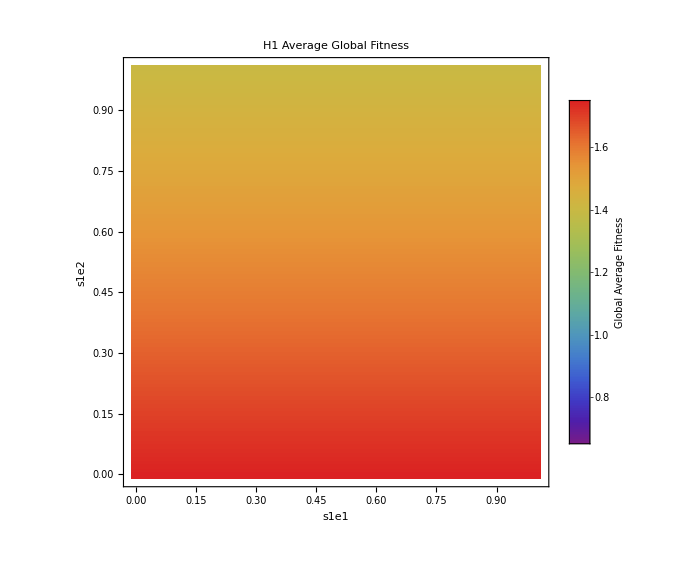
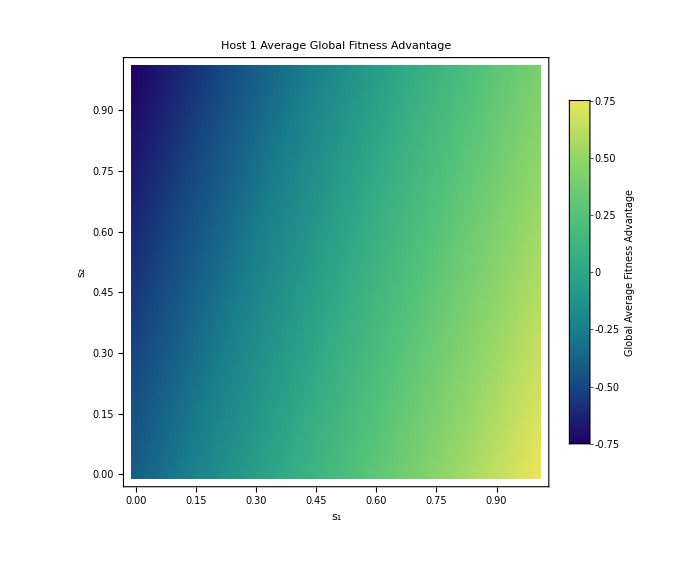
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pi1=0.1;
pi2=0.7;
fitnessfxn3[1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2]
```

Initially near global genotypic match:

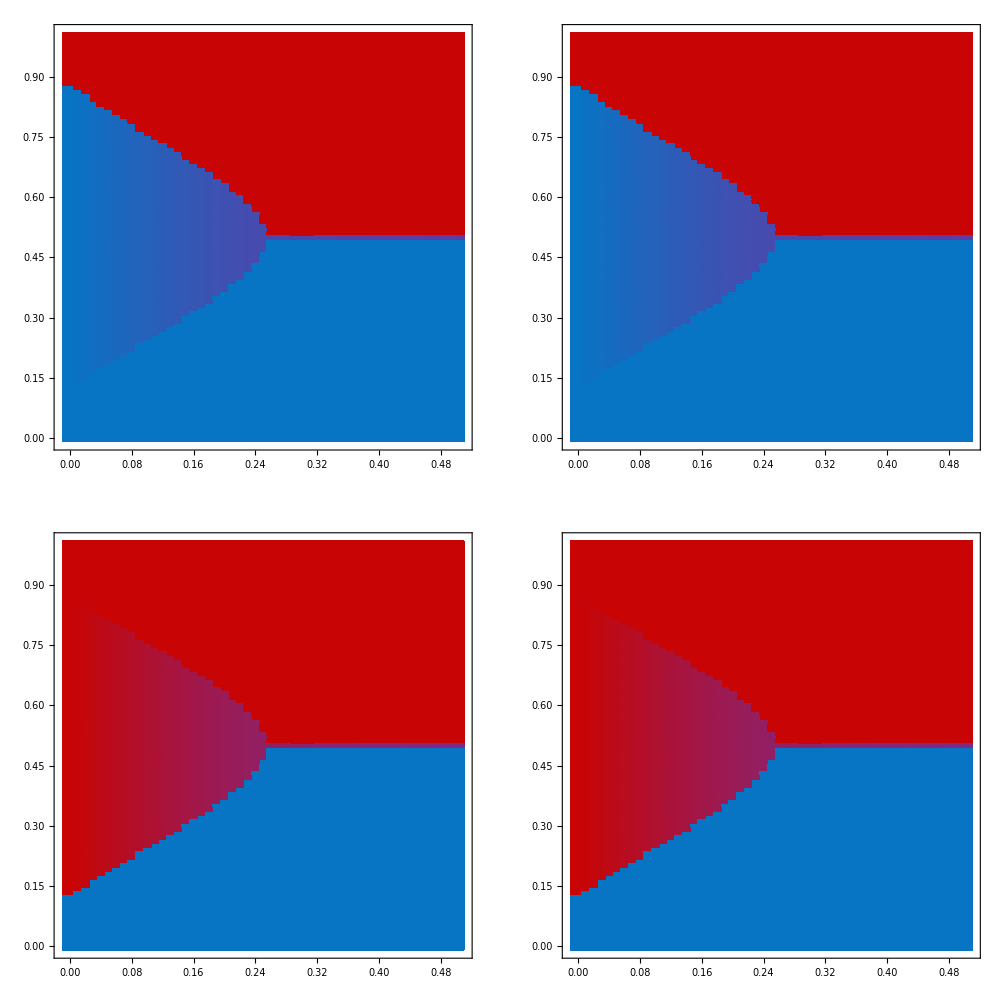
{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.1;(*stand in for ΔHms and ΔSmh*)
pi2=0.7;(*stand in for ΔHgh and ΔSgs*)
a=PlotWFN[h1e10,h1e10,h1e10,h1e10,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
(*Inelegant functions for annotating equilibria directly on figure: *)
(*Export["dummy.png",%];
b=Import["dummy.png"];

fontsize=60;
text={Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["GM",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],Graphics[Text[Style["RMS",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["RMS",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["RMS",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],
Graphics[Text[Style["RMS",Directive[FontSize-> fontsize],FontFamily->"Times",FontColor-> White]]],Graphics[Text[Style["RMS -Reverse Migration Selection",Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["Balance",Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["GM -Global Genotypic Match",Directive[FontSize-> 40],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["a)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["b)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],
Graphics[Text[Style["c)",Directive[FontSize-> 32],FontFamily->"Times",FontColor-> Black]]],Graphics[Text[Style["d)",Directive[FontSize->32],FontFamily->"Times",FontColor-> Black]]]};

afl=0
us=0.05;
ds=0.17;
ds2=0.085;
x1=0.3;
x2=0.72;
y1=0.78+us;
y2=0.33+0.035+us;
ls=0.12;
top={Scaled[{x1,y1+afl}],Scaled[{x2,y1+afl}],Scaled[{x1,y2+afl}],Scaled[{x2,y2+afl}]};
bottom={Scaled[{x1,y1-ds+afl}],Scaled[{x2,y1-ds+afl}],Scaled[{x1,y2-ds+afl}],Scaled[{x2,y2-ds+afl}]};
middle={Scaled[{x1-ls,y1-ds2+afl}],Scaled[{x2-ls-0.015,y1-ds2+afl}],Scaled[{x1-ls,y2-ds2+afl}],Scaled[{x2-ls-0.015,y2-ds2+afl}]};
legend={Scaled[{0.25,0.075}],Scaled[{0.25,0.04}],Scaled[{0.74,0.075}]};
panels={Scaled[{0.1,0.94}],Scaled[{0.5,0.94}],Scaled[{0.1,0.53}],Scaled[{0.5,0.53}]};
ImageCompose[b,text,Join[top,bottom,middle,legend,panels]]
Export["GXG>GXE.png",%]*)
```

Initially near global genotypic mismatch:

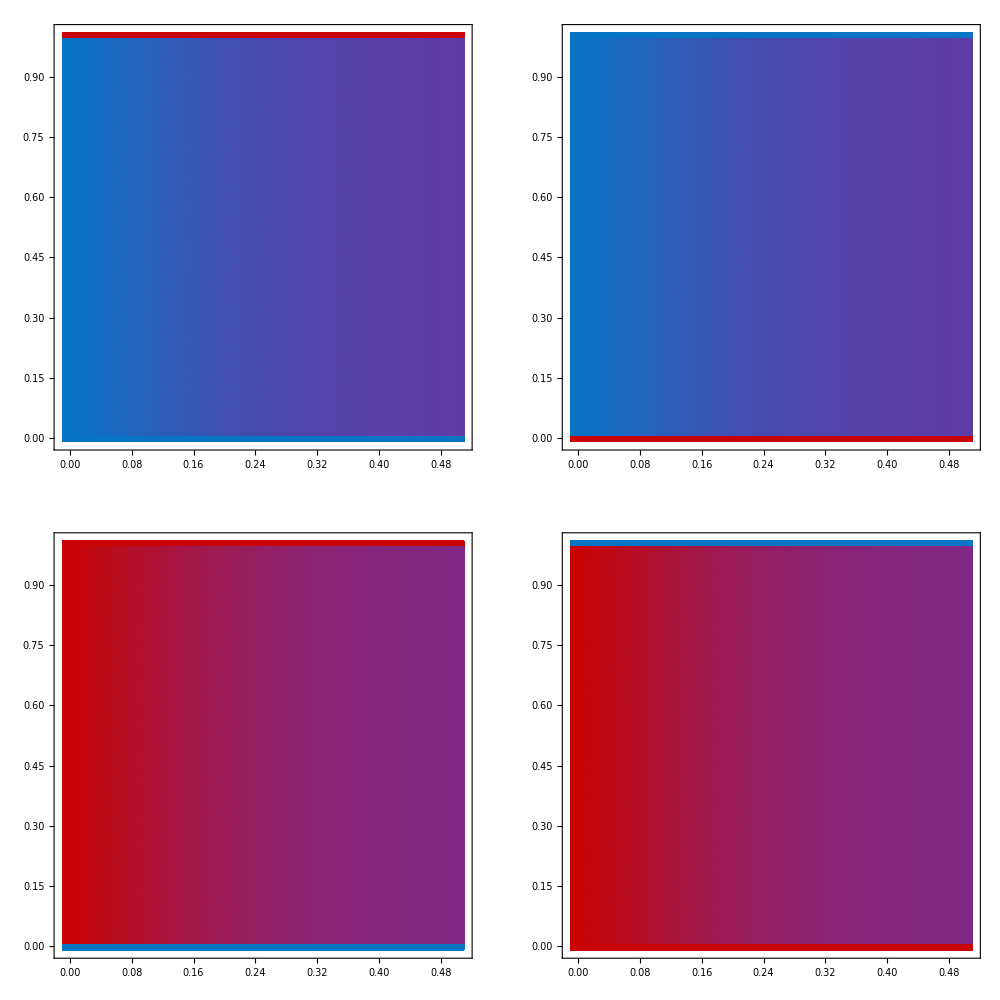
{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.2;(*stand in for ΔHms and ΔSmh*)
pi2=0.35;(*stand in for ΔHgh and ΔSgs*)
PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
```

Initially near internal equilibria:

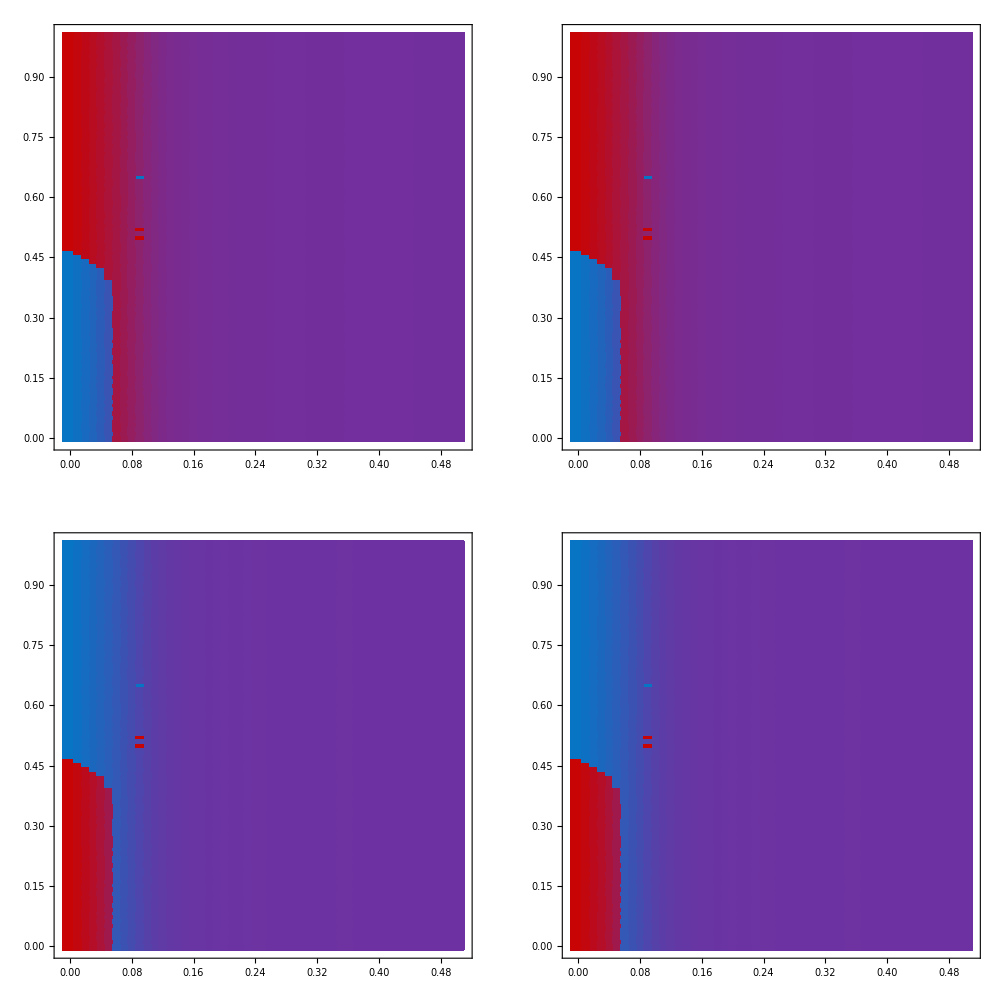
{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.2;(*stand in for ΔHms and ΔSmh*)
pi2=0.35;(*stand in for ΔHgh and ΔSgs*)
PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
```

All initial conditions:

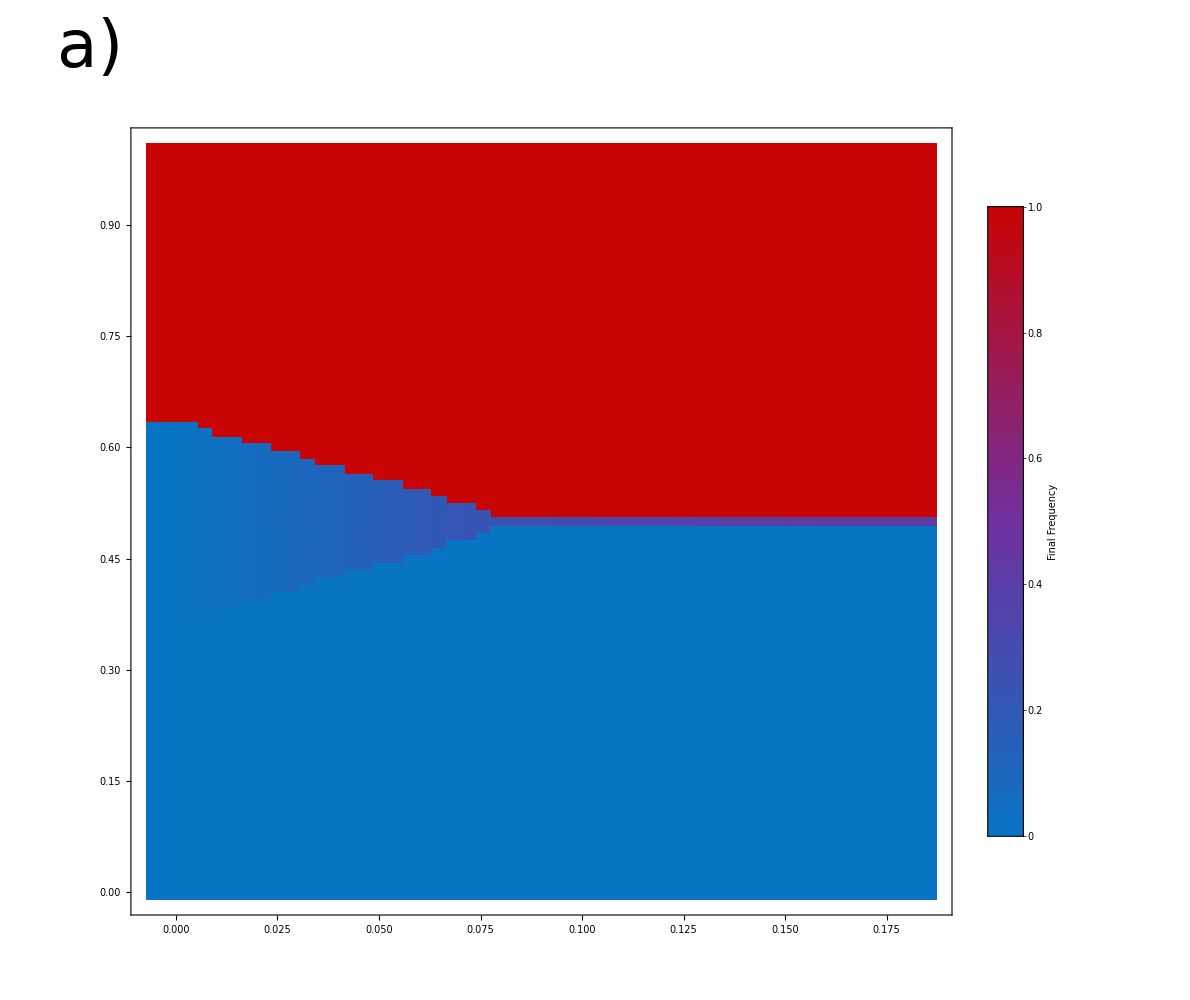
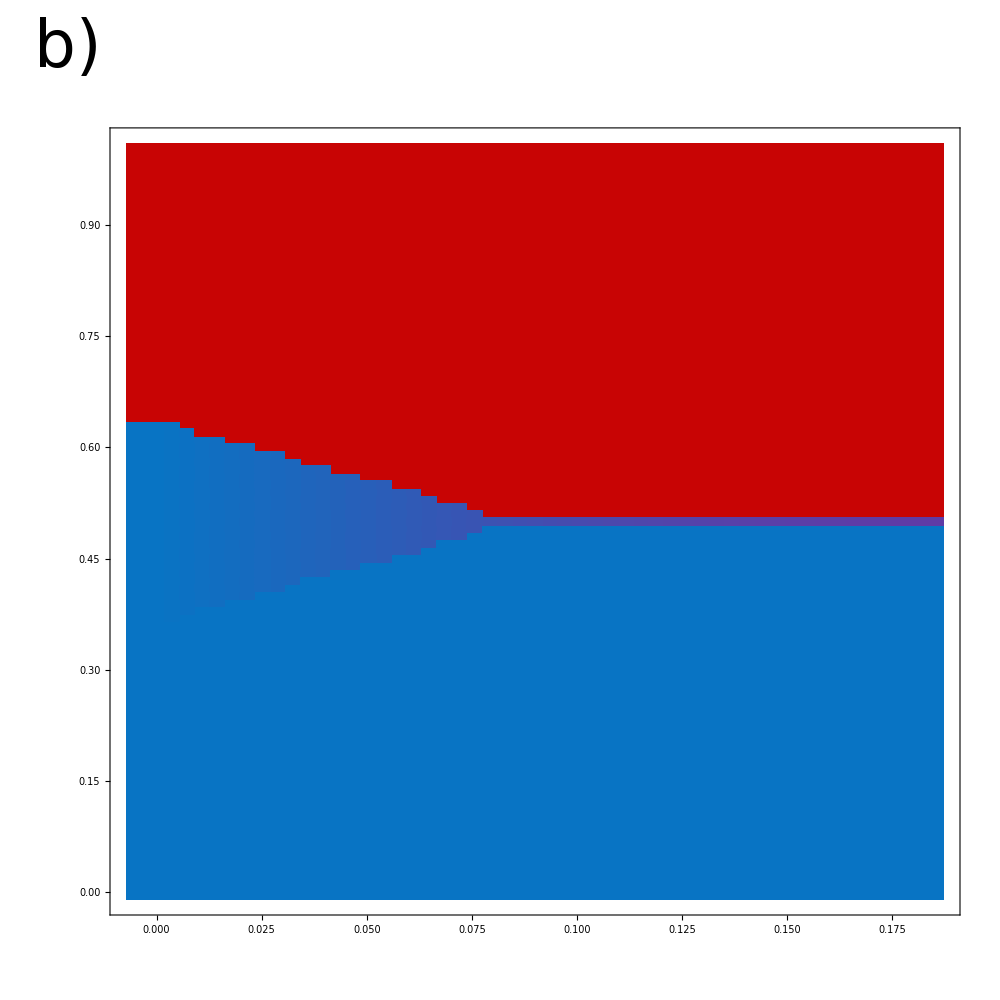
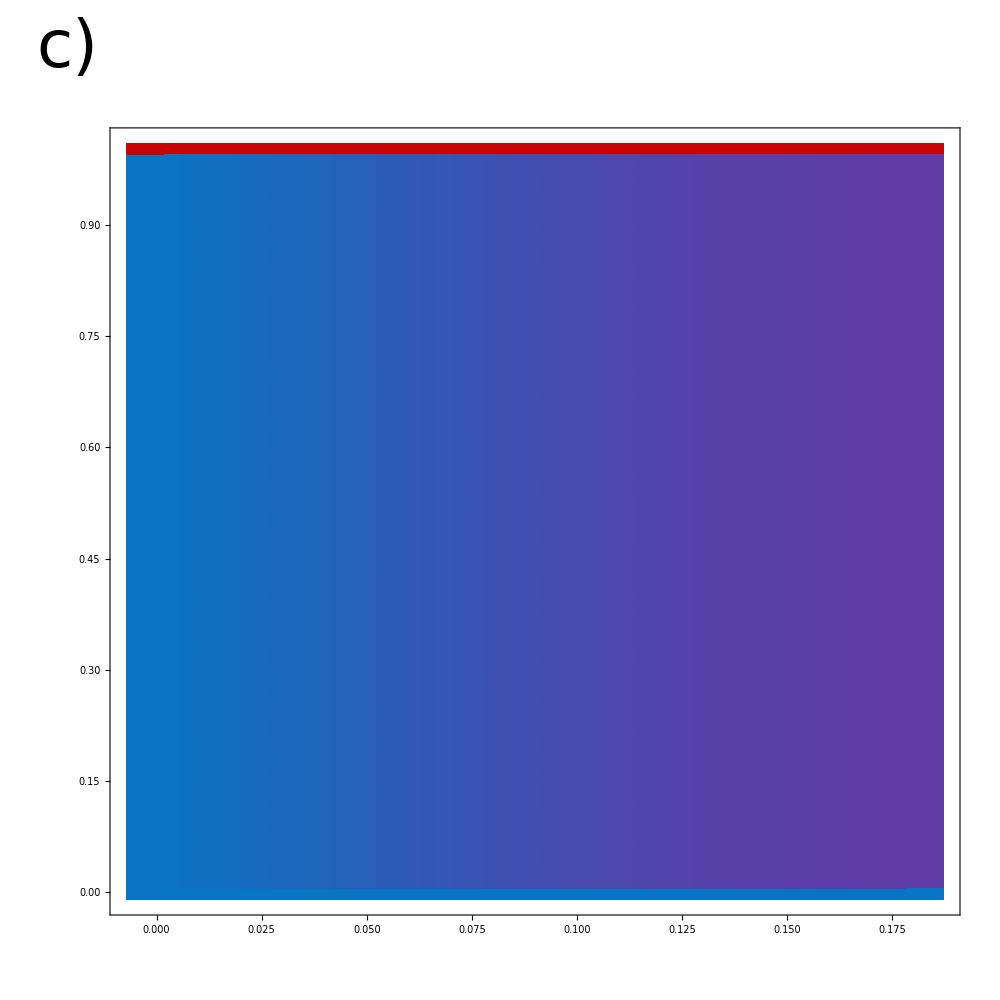
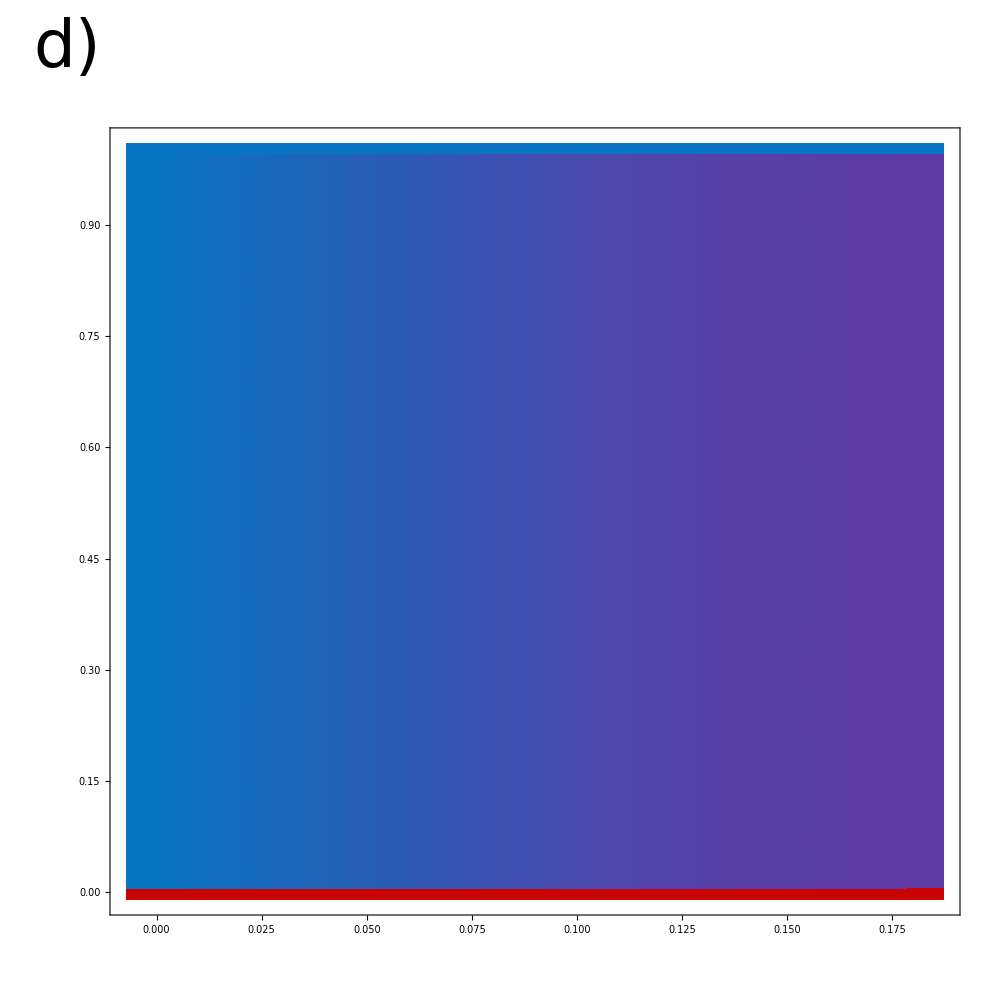
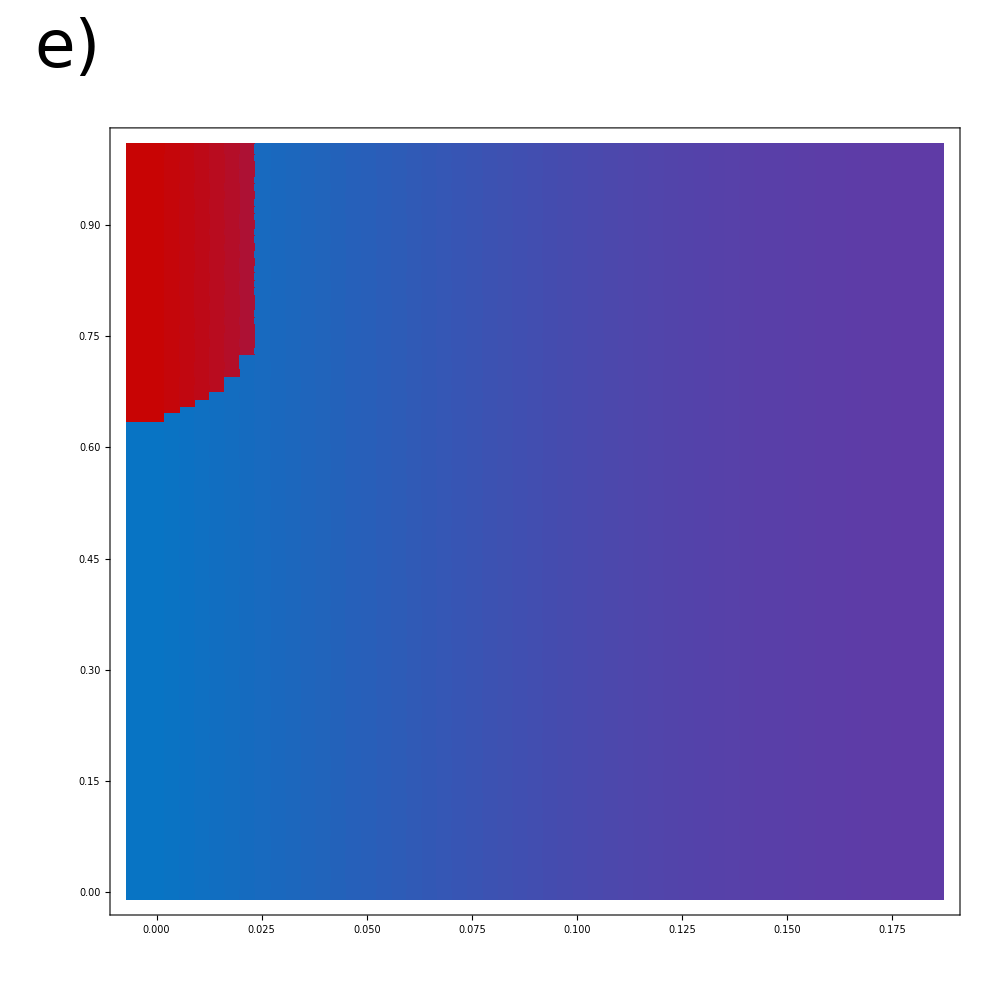
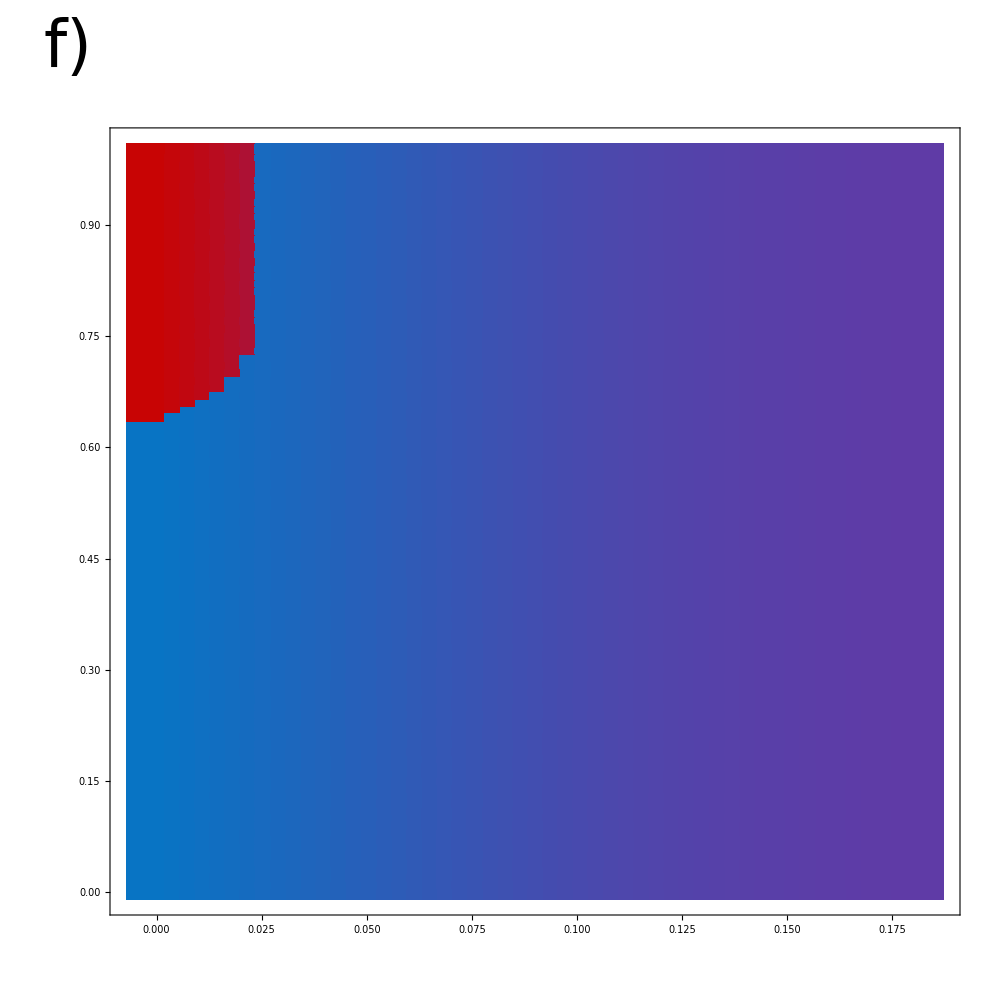
{Initially near global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially near global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially near internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

```mathematica
ΔHms=0.2;
ΔHgh=0.35;
ΔSmh=0.2;
ΔSgs=0.35;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,Abs[ΔHms-ΔHgh]*1.2]
(*Export["GXE<GXG.png",%]*)
```

#### Testing which internal equilibrium is stable at high dispersal:

At high dispersal, these simulations suggest that migration selection balance is locally  stable if ΔHms +ΔSmh > ΔHgh + ΔSgs, and reverse migration selection balance is locally stable if ΔHms +ΔSmh < ΔHgh + ΔSgs . We also have to vary whether ΔHms > ΔHgh and ΔSmh >ΔSgs to confirm our intuition.

ΔHms +ΔSmh > ΔHgh + ΔSgs 
ΔHms>ΔHgh
ΔSmh>ΔSgs
 favors migration selection balance

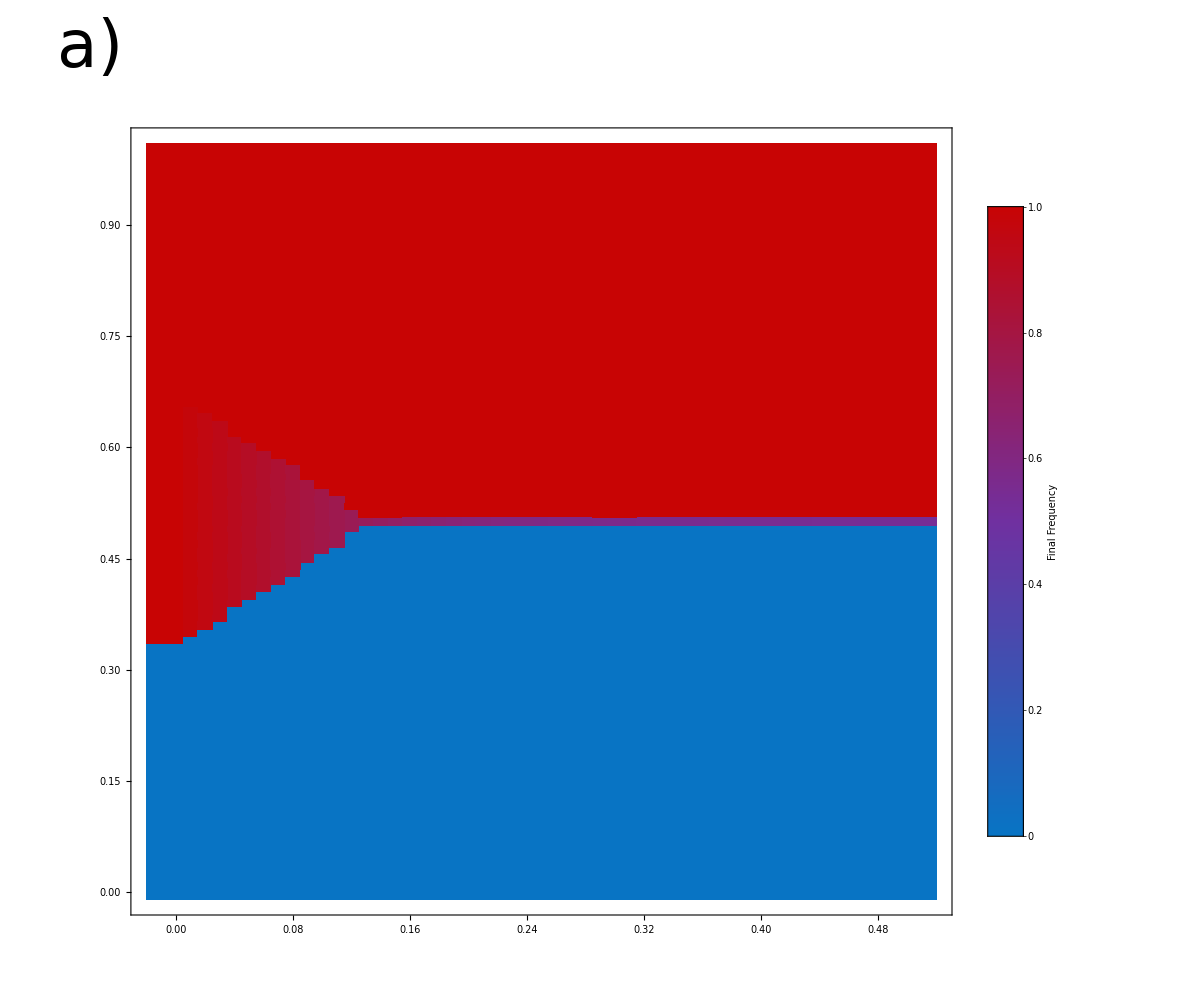
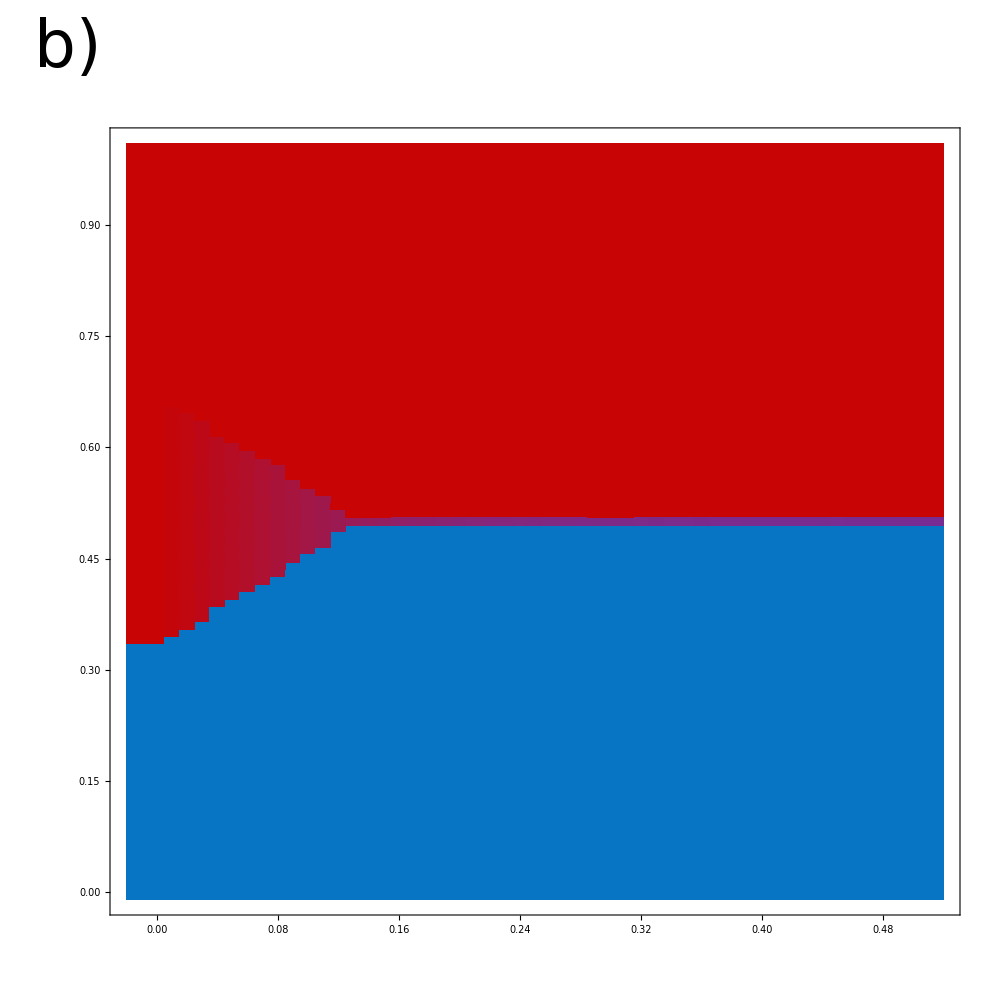
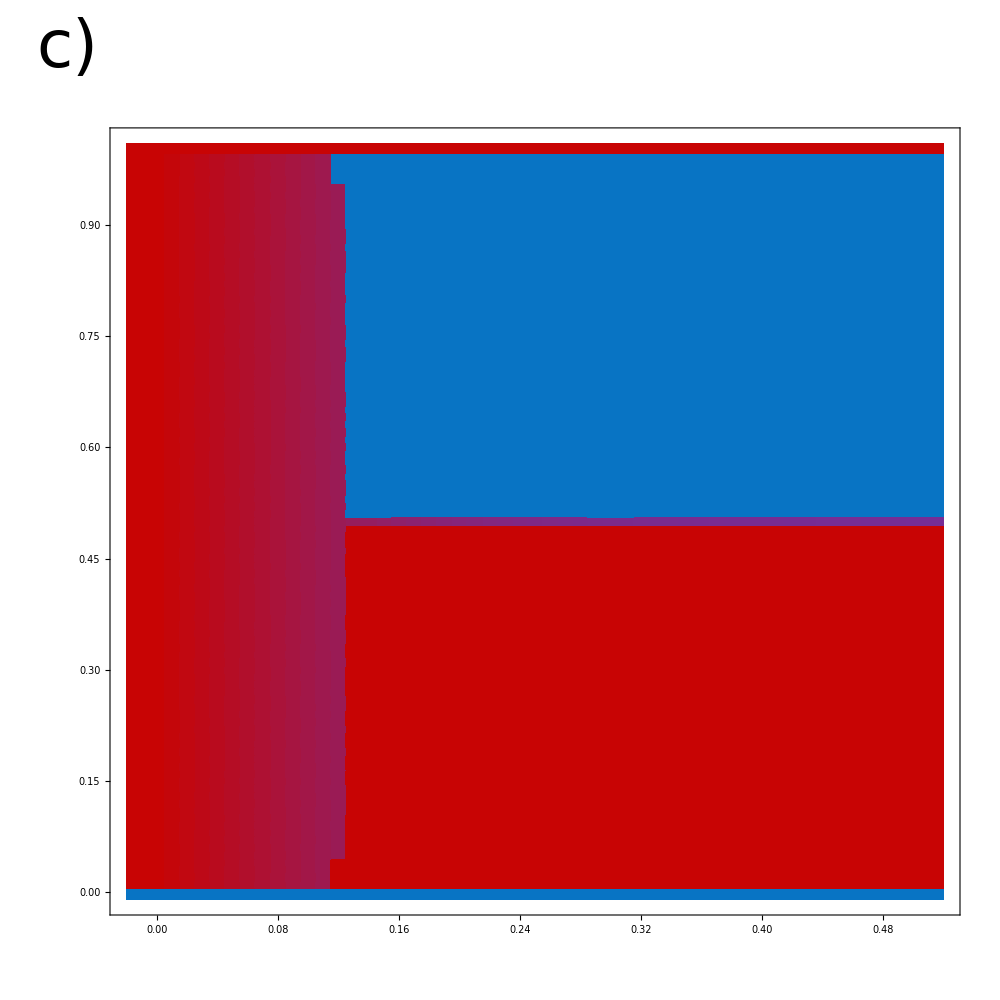
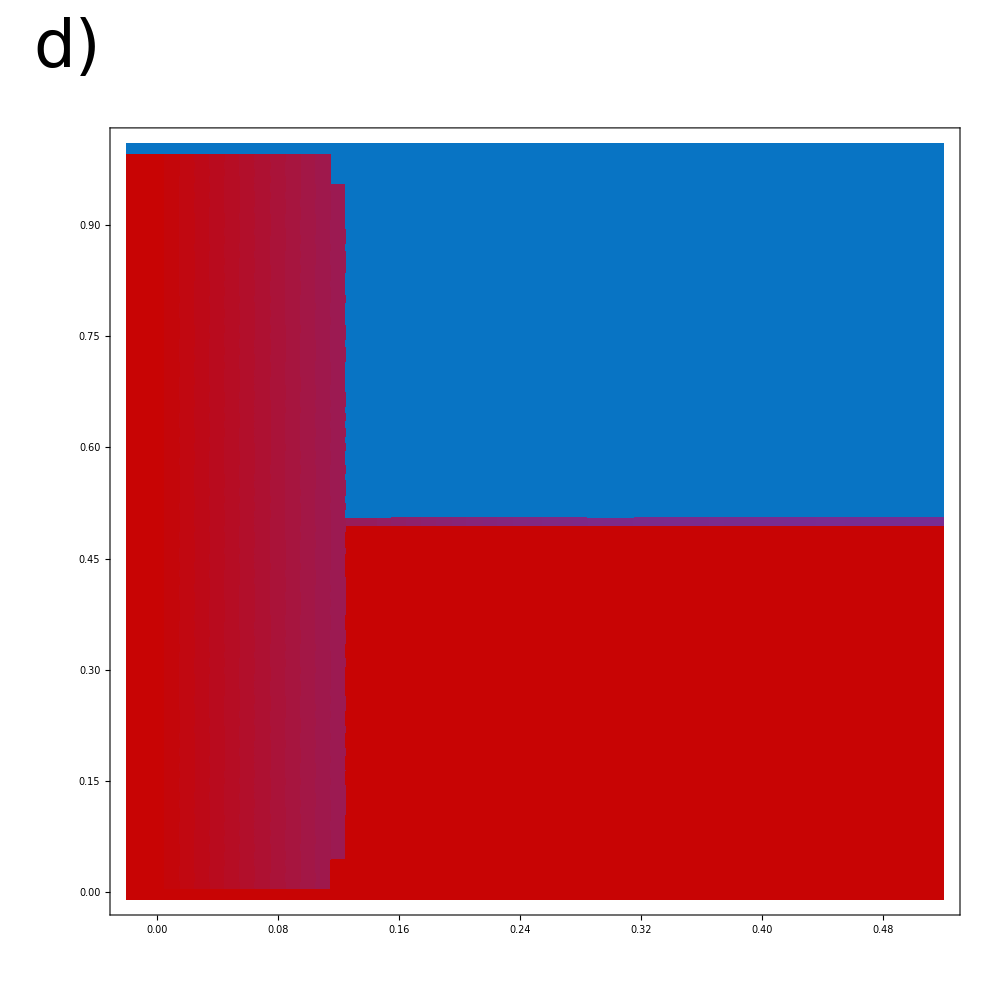
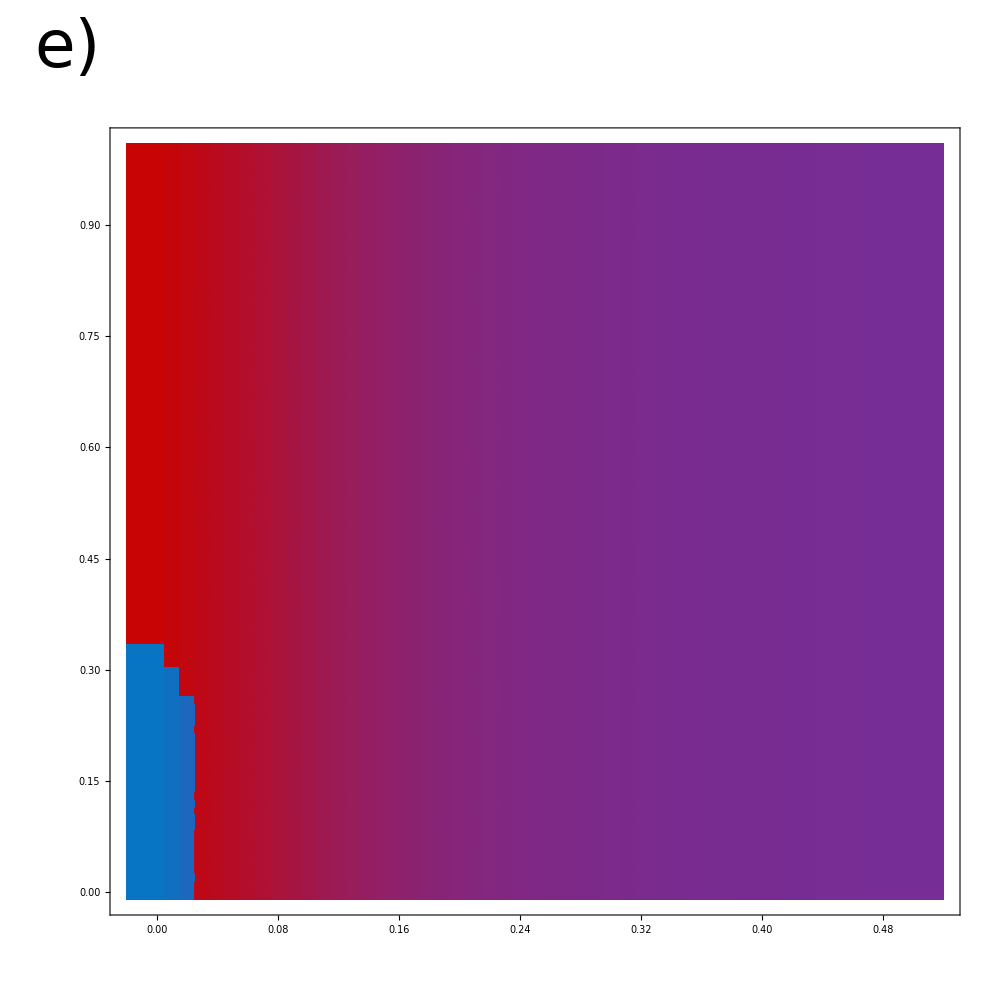
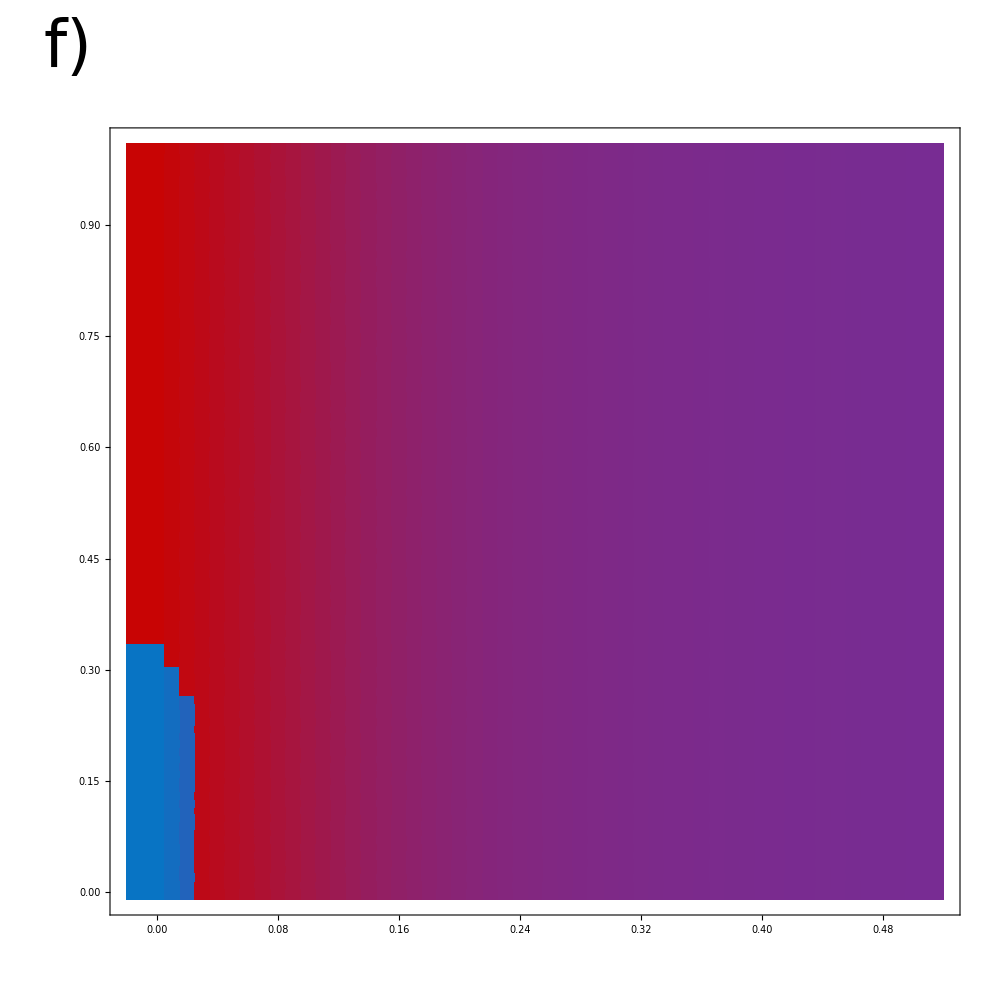
{Initially favors global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially favors global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially favors internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

```mathematica
ΔHms=0.5;(*stand in for ΔHms and ΔSmh*)
ΔHgh=0.3;(*stand in for ΔHgh and ΔSgs*)
ΔSmh=0.5;
ΔSgs=0.2;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,0.5]
(*Export["ΔHms=0.2&ΔHgh=0.35.png",%]*)
```

ΔHms +ΔSmh > ΔHgh + ΔSgs
ΔHms<ΔHgh
ΔSmh>ΔSgs
 favors migration selection balance

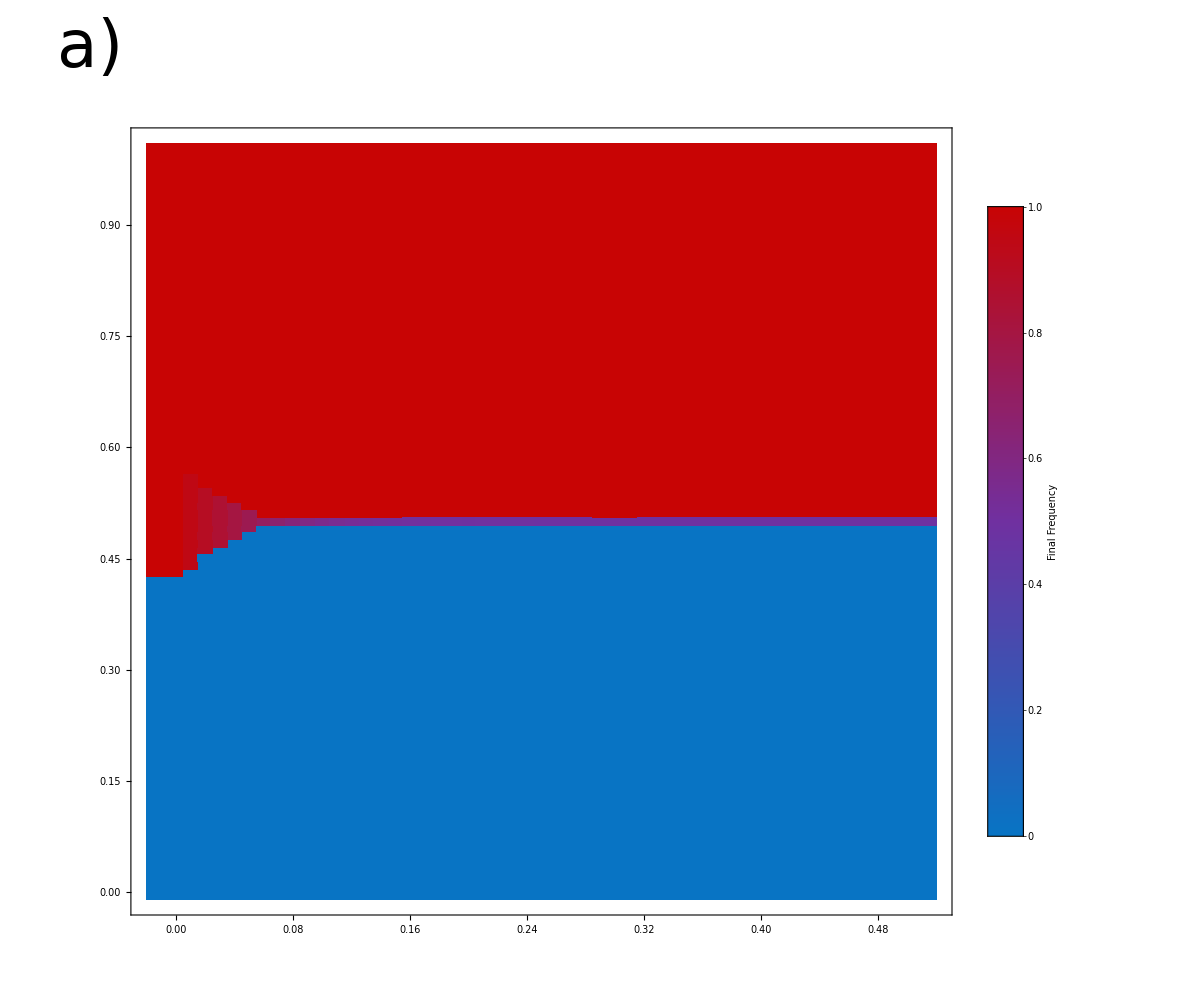
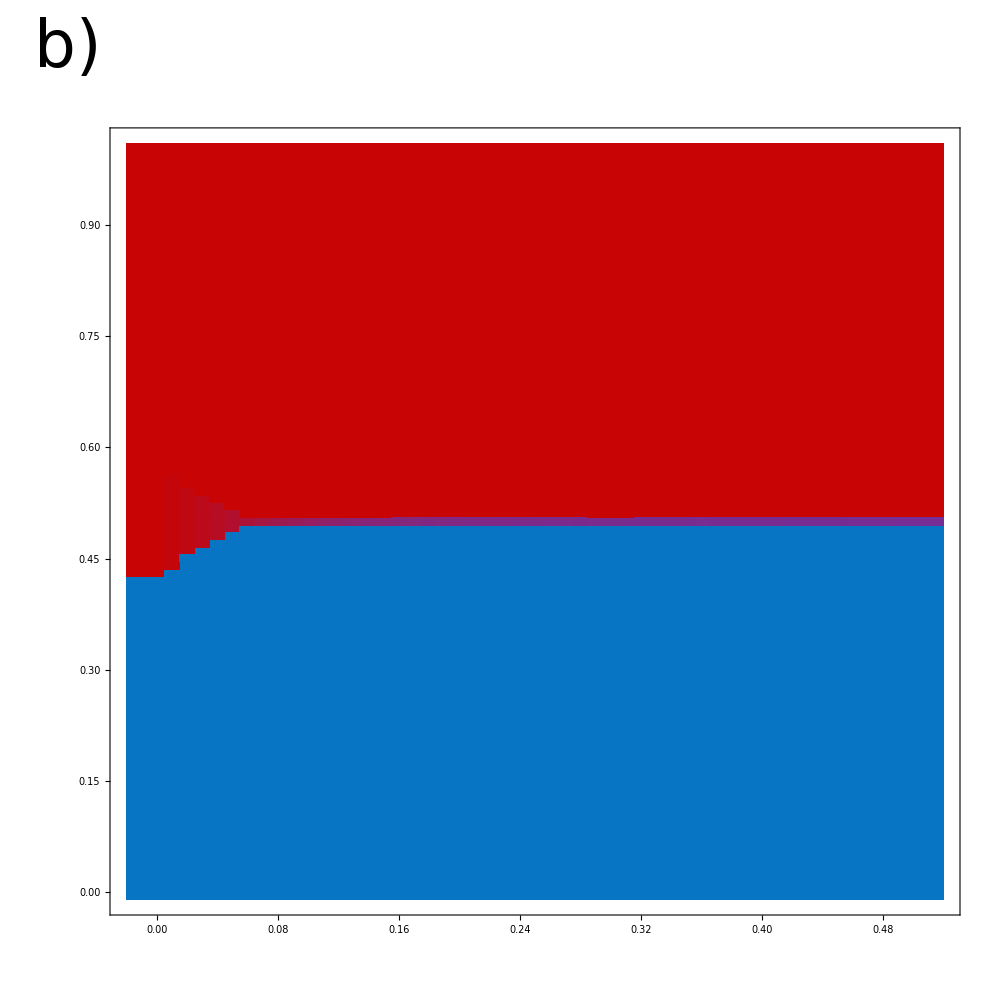
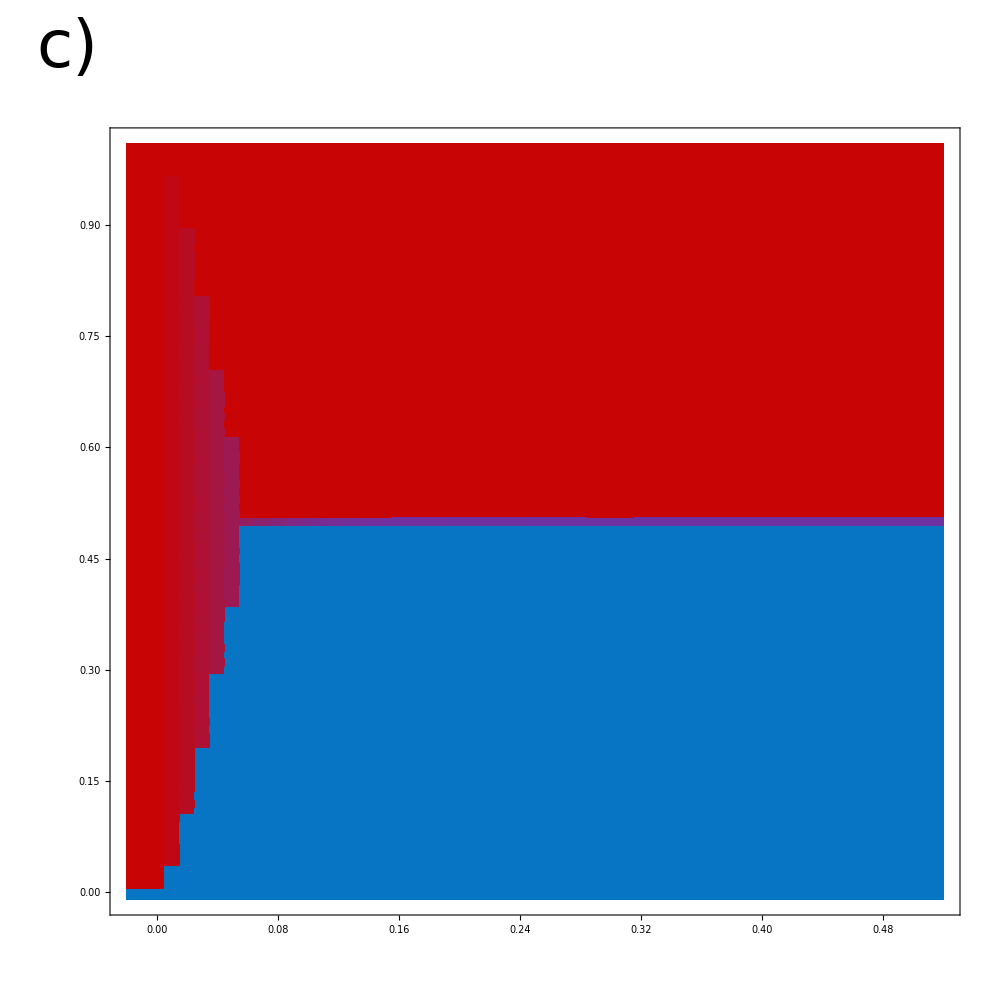
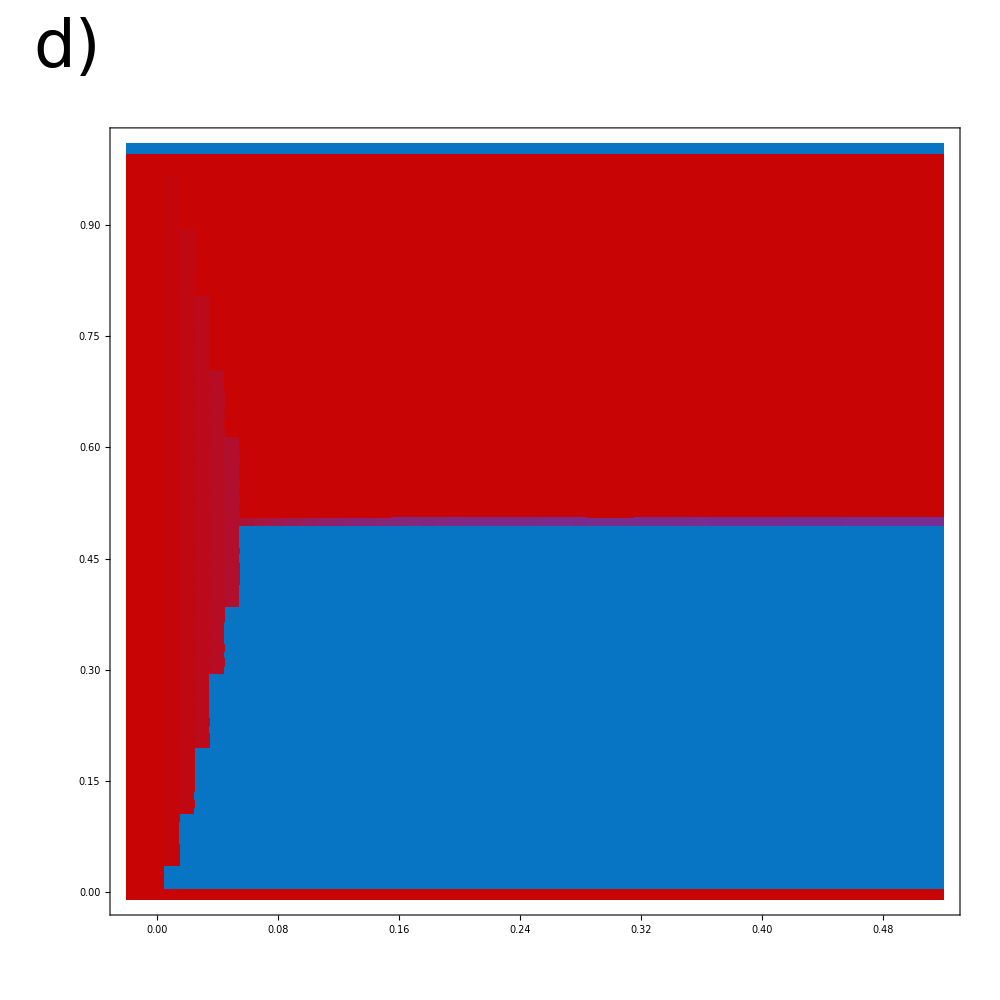
{Initially favors global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially favors global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially favors internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

```mathematica
ΔHms=0.2;(*stand in for ΔHms and ΔSmh*)
ΔHgh=0.3;(*stand in for ΔHgh and ΔSgs*)
ΔSmh=0.5;
ΔSgs=0.2;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,0.5]
(*Export["ΔHms=0.2&ΔHgh=0.35.png",%]*)
```

ΔHms +ΔSmh < ΔHgh + ΔSgs
ΔHms<ΔHgh
ΔSmh>ΔSgs
 favors reverse migration selection balance

```mathematica
ΔHms=0.2;(*stand in for ΔHms and ΔSmh*)
ΔHgh=0.5;(*stand in for ΔHgh and ΔSgs*)
ΔSmh=0.3;
ΔSgs=0.2;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,0.5]
(*Export["ΔHms=0.2&ΔHgh=0.35.png",%]*)
```

{Initially favors global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially favors global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially favors internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

ΔHms +ΔSmh < ΔHgh + ΔSgs
ΔHms<ΔHgh
ΔSmh<ΔSgs
favors reverse migration selection balance

```mathematica
ΔHms=0.2;(*stand in for ΔHms and ΔSmh*)
ΔHgh=0.5;(*stand in for ΔHgh and ΔSgs*)
ΔSmh=0.2;
ΔSgs=0.4;
PlotWFN3[1.8,1,1-ΔHgh,1.8-ΔHms,1.8,1,1.8-ΔSmh,1-ΔSgs,0.5]
(*Export["ΔHms=0.2&ΔHgh=0.35.png",%]*)
```

{Initially favors global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially favors global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially favors internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

### When matching the environment matters more than matching genotypes (GXE>GXG)

```mathematica
(*You can run these functiosn to see dynamics in every single patch*)

pi1=0.1;(*stand in for ΔHms and ΔSmh*)
pi2=0.7;(*stand in for ΔHgh and ΔSgs*)
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
(*Initially near global genotypic mismatch: *)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
```

We can test stability near each of the internal equilibria with just one function:

```mathematica
pi1=0.7;(*stand in for ΔHms and ΔSmh*)
pi2=-0.1;(*stand in for ΔHgh and ΔSgs*)
PlotWFN3[1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5]
(*Export["pi1=0.7&pi2=-0.1.png",%]*)
```

{Initially near global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially near global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially near internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

#### GXE>GXG for one partner, GXE<GXG for the other.

Our analysis predicts that the same equilibria should be locally stable under these conditions.

```mathematica
pi1=0.3;
pi2=-0.2;
psi1=0.3;
psi2=0.2;
PlotWFN3[1,1,1-pi2,1-pi1,1,1,1-psi1,1-psi2,0.75]
(*Export["pi1=0.3&pi2=-0.2&psi1=0.3&psi2=0.2.png",%]*)
```

{Initially near global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially near global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially near internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

### When matching the environment matters more for one partner, but not the other (GXE>>GXG for just one partner)

#### GXE>>GXG for one partner, GXE<GXG for the other

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=0.1;
(*Value of matched internal equilibrium*)
{matchedintplot=Plot[{1-d/pi1,d/pi1,1-d/psi1,d/psi1},{d,0,0.5},PlotStyle->{Red,Blue,Green,Purple},PlotLabel-> "Matched Internal Equilibrium",PlotLabels->{"1-d/Δπ1 in matched env","d/Δπ1in mismatched env","1-d/Δψ1 in matched env","d/Δψ1in mismatched env"}, ImageSize-> Large],
(*Value of mis-matched internal equilibrium*)
mismatchedintplot=Plot[{d/pi2,1-d/pi2,d/psi2,1-d/psi2},{d,0,0.5},PlotStyle->{Red,Blue,Green,Purple},PlotLabel-> "Mismatched Internal Equilibrium",PlotLabels->{"d/Δπ2in matched env","1-d/Δπ2 in mismatched env","d/Δψ2 in matched env","1-d/Δψ2in mismatched env"}, ImageSize-> Large]}
{(*Value of Routh-Hurwitz criterion for mismatched boundary equilibrium*)
mismatchedrouthhurwitz=Plot[{2d-(pi1+pi2),pi1*pi2-d(pi1+pi2),2d-(psi1+psi2),psi1*psi2-d(psi1+psi2)},{d,0,0.5},PlotLabel-> "Routh-Hurwitz mismatched boundary",PlotLabels->{"H a1","H a2","S a1","S a2"}, ImageSize-> Medium],
(*Value of Routh-Hurwitz criterion for matched boundary equilibrium*)
matchedrouthhurwitz=Plot[{2d+(pi1+pi2),pi1*pi2+d(pi1+pi2),2d+(psi1+psi2),psi1*psi2+d(psi1+psi2)},{d,0,1},PlotLabel-> "Routh-Hurwitz matched boundary",PlotLabels->{"H a1","H a2","S a1","S a2"}, ImageSize-> Medium]}
```

{-Graphics-,-Graphics-}

{-Graphics-,-Graphics-}

```mathematica
fitnessfxn3asym[HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]:=
{(*Host 1 Fitness*)
w1=s1*HM+(1-s1)*Hh;
w2=s1*Hg+(1-s1)*Hs;
Plot[{w1,w2,Mean[{w1,w2}]},{s1,0,1},AxesLabel->{"symbiont 1 frequency","Host 1 fitness"},PlotLabel-> "host 1 local fitness",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium],
(*Host 1 Fitness variation in Symbiont Frequency*)
averageWg1=Table[{se1,se2,w1=se1*HM+(1-se1)*Hh;w2=se2*Hg+(1-se2)*Hs;Mean[{w1,w2}]},{se1, 0,1,0.01},{se2,0,1,0.01}];
averageWg1p=Flatten[averageWg1,1];
ListDensityPlot[averageWg1,Frame->True,FrameLabel->{"s1e1","s1e2"},PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "Rainbow",InterpolationOrder-> 0,PlotLabel-> "H1 Average Global Fitness",PlotLegends->Placed[BarLegend[{"Rainbow",{Min[averageWg1p[[All,3]]],Max[averageWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Average Fitness",LegendFunction->"Panel"],Right],ImageSize->Medium],
(*Host 1 Fitness advantage*)
w1=s1*HM+(1-s1)*Hh-(s1*Hs+(1-s1)*Hg);
w2=s1*Hg+(1-s1)*Hs-(s1*Hh+(1-s1)*HM);
Plot[{w1,w2,Mean[{w1,w2}]},{s1,0,1},AxesLabel->{"symbiont 1 frequency","Host 1 fitness"},PlotLabel-> "host 1 local fitness advantage",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium],
averageΔWg1=Table[{se1,se2,w1=se1*HM+(1-se1)*Hh-(se1*Hs+(1-se1)*Hg);w2=se2*Hg+(1-se2)*Hs-(se1*Hh+(1-se1)*HM);Mean[{w1,w2}]},{se1, 0,1,0.01},{se2,0,1,0.01}];
averageΔWg1p=Flatten[averageΔWg1,1];
ListDensityPlot[averageΔWg1p,Frame->True,FrameLabel->{"s1e1","s1e2"},PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "BlueGreenYellow",InterpolationOrder-> 0,PlotLabel-> "H1 Average Global Fitness Advantage",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{Min[averageΔWg1p[[All,3]]],Max[averageΔWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Average Host Fitness Advantage",LegendFunction->"Panel"],Right],ImageSize->Medium],
(*Symbiont 1 Fitness*)
w1=h1*SM+(1-h1)*Ss;
w2=h1*Sg+(1-h1)*Sh;
Plot[{w1,w2,Mean[{w1,w2}]},{h1,0,1},AxesLabel->{"host 1 frequency","Symbiont 1 fitness"},PlotLabel-> "symbiont 1 local fitness",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium],
(*Symbiont 1 Fitness variation in Symbiont Frequency*)
averageWg1=Table[{he1,he2,w1=he1*SM+(1-he1)*Ss;w2=he2*Sg+(1-he2)*Sh;Mean[{w1,w2}]},{he1, 0,1,0.01},{he2,0,1,0.01}];
averageWg1p=Flatten[averageWg1,1];
ListDensityPlot[averageWg1,Frame->True,FrameLabel->{"h1e1","h1e2"},PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "Rainbow",InterpolationOrder-> 0,PlotLabel-> "S1 Average Global Fitness",PlotLegends->Placed[BarLegend[{"Rainbow",{Min[averageWg1p[[All,3]]],Max[averageWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Average Symbiont Fitness",LegendFunction->"Panel"],Right],ImageSize->Medium],
(*Host 1 Fitness advantage*)
w1=h1*SM+(1-h1)*Ss-(h1*Sg+(1-h1)*Sh);
w2=h1*Sg+(1-h1)*Sh-(h1*SM+(1-h1)*Ss);
Plot[{w1,w2,Mean[{w1,w2}]},{h1,0,1},AxesLabel->{"host 1 frequency","Symbiont 1 fitness"},PlotLabel-> "Symbiont 1 local fitness advantage",PlotLabels->{"e1","e2","Mean"},ImageSize->Medium],
averageΔWg1=Table[{he1,he2,w1=he1*SM+(1-he1)*Ss-(he1*Sg+(1-he1)*Sh);w2=he2*Sg+(1-he2)*Sh-(he2*SM+(1-he2)*Ss);Mean[{w1,w2}]},{he1, 0,1,0.01},{he2,0,1,0.01}];
averageΔWg1p=Flatten[averageΔWg1,1];
ListDensityPlot[averageΔWg1p,Frame->True,FrameLabel->{"h1e1","h1e2"},PlotRange->{{-0.01,1.01},{-0.01,1.01},All},AspectRatio->1,ColorFunction-> "BlueGreenYellow",InterpolationOrder-> 0,PlotLabel-> "S1 Average Global Fitness Advantage",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{Min[averageΔWg1p[[All,3]]],Max[averageΔWg1p[[All,3]]]}},LegendMargins->{{0,0},{10,5}},LegendLabel->"Global Symbiont Average Fitness Advantage",LegendFunction->"Panel"],Right],ImageSize->Medium]
}
```

```mathematica
Hms=0.3;
Hgs=-0.7;
Smh=0.3;
Sgh=0.1;
fitnessfxn3asym[1.1,1,1-Hgs,1.1-Hms,1.1,1,1.1-Smh,1-Sgh]
				(*[HM_,Hg_,Hh_,Hs_, SM_, Sg_,Sh_,Ss_]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

You can check full dynamics with these three functions:

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=0.1;

(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
(*Initially near global genotypic mismatch: *)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
```

{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=0.1;
PlotWFN3[1,1,1-pi2,1-pi1,1,1,1-psi1,1-psi2,0.5]
(*Export["pi1=0.3&pi2=-0.7&psi1=0.3&psi2=0.1.png",%]*)
```

{Initially near global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially near global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially near internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

#### GXE>>GXG for one partner, GXE>GXG for the other.

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=-0.1;
(*Value of matched internal equilibrium*)
matchedintplot=Plot[{1-d/pi1,d/pi1,1-d/psi1,d/psi1},{d,0,0.5},PlotStyle->{Red,Blue,Green,Purple},PlotLabel-> "Matched Internal Equilibrium",PlotLabels->{"1-d/Δπ1 in matched env","d/Δπ1in mismatched env","1-d/Δψ1 in matched env","d/Δψ1in mismatched env"}, ImageSize-> Large]
(*Value of mis-matched internal equilibrium*)
mismatchedintplot=Plot[{d/pi2,1-d/pi2,d/psi2,1-d/psi2},{d,0,0.5},PlotStyle->{Red,Blue,Green,Purple},PlotLabel-> "Mismatched Internal Equilibrium",PlotLabels->{"d/Δπ2in matched env","1-d/Δπ2 in mismatched env","d/Δψ2 in matched env","1-d/Δψ2in mismatched env"}, ImageSize-> Large]
(*Value of Routh-Hurwitz criterion for mismatched boundary equilibrium*)
mismatchedrouthhurwitz=Plot[{2d-(pi1+pi2),pi1*pi2-d(pi1+pi2),2d-(psi1+psi2),psi1*psi2-d(psi1+psi2)},{d,0,0.5},PlotLabel-> "Routh-Hurwitz mismatched boundary",PlotLabels->{"H a1","H a2","S a1","S a2"}]
(*Value of Routh-Hurwitz criterion for matched boundary equilibrium*)
matchedrouthhurwitz=Plot[{2d+(pi1+pi2),pi1*pi2+d(pi1+pi2),2d+(psi1+psi2),psi1*psi2+d(psi1+psi2)},{d,0,0.5},PlotLabel-> "Routh-Hurwitz matched boundary",PlotLabels->{"H a1","H a2","S a1","S a2"}]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

All patches:

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=-0.1;
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
(*Initially near global genotypic mismatch: *)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-psi1,1-psi2,0.5,0.01]
```

{-Graphics-Initial FrequencyDispersal}

{-Graphics-Initial FrequencyDispersal}

{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.3;
pi2=-0.7;
psi1=0.3;
psi2=-0.1;
PlotWFN3[1,1,1-pi2,1-pi1,1,1,1-psi1,1-psi2,0.75]
Export["pi1=0.3&pi2=-0.7&psi1=0.3&psi2=-0.1.png",%]
```

{Initially favors global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially favors global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially favors internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}

pi1=0.3&pi2=-0.7&psi1=0.3&psi2=-0.1.png

### When matching the environment matters much more than matching genotypes (GXE>>GXG).

```mathematica
pi1=0.1;
pi2=-0.7;
fitnessfxnSym[1.1,1,1-pi2,1.1-pi1,1.1,1,1.1-pi1,1-pi2,pi1,pi2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pi1=0.1;
pi2=-0.7;
fitnessfxn3[1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

All patches:

```mathematica
pi1=0.1;
pi2=-0.7;
(*Initially near global genotypic match: *)PlotWFN[h1e10,h1e10,h1e10,h1e10,1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
(*Initially near global genotypic mismatch: *)PlotWFN[h1e10,h1e10,(1-h1e10),(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
(*Initially near internal equilibria:*)PlotWFN[h1e10,(1-h1e10),h1e10,(1-h1e10),1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5,0.01]
	         	(*[h1e10_,h1e20_,s1e10_,s1e20_,HM,Hg,  Hh,   Hs,   SM,Sg_, Sh,   Ss]*)
```

{-Graphics-Initial FrequencyDispersal}

{-Graphics-Initial FrequencyDispersal}

{-Graphics-Initial FrequencyDispersal}

```mathematica
pi1=0.1;
pi2=-0.7;
PlotWFN3[1.8,1,1-pi2,1.8-pi1,1.8,1,1.8-pi1,1-pi2,0.5]
(*Export["pi1=0.1&pi2=-0.7.png",%]*)
```

{Initially near global genotypic match equilibria  | 
-Graphics- | -Graphics-
Initially near global genotypic mismatch equilibria | 
-Graphics- | -Graphics-
Initially near internal equilibria | 
-Graphics- | -Graphics-Initial FrequencyDispersal}